```mathematica
Import["C:\\Users\\jhenry1\\Documents\\GitHub\\QM_prisoners_dilemma\\Mathematica\\StrategySpaces.wl"]
Import["C:\\Users\\jhenry1\\Documents\\GitHub\\QM_prisoners_dilemma\\Mathematica\\QPD_dynamics.wl"]
Import["C:\\Users\\jhenry1\\Documents\\GitHub\\QM_prisoners_dilemma\\Mathematica\\DiscreteNashEqulibrium.wl"]
```

```mathematica
σ0= ({{1, 0}, {0, 1}});
σ1 = ({{0, 1}, {1, 0}});
σ2 = ({{0, 1}, {-1, 0}});
σ3 = ({{1, 0}, {0, -1}});
s =  ({{1, 0}, {0, I}});
```

```mathematica
D4 = {σ0,σ3,s,s.σ3,s.σ1,s.σ2,σ1,σ2};
D4Sym = {"σ_0","σ_z","S","Sσ_z","Sσ_x","Sσ_y","σ_x","σ_y"};
```

```mathematica
alicesScores/.{γ->0}//MatrixForm
```

(3 | 3 | 3 | 3 | 0 | 0 | 0 | 0
3 | 3 | 3 | 3 | 0 | 0 | 0 | 0
3 | 3 | 3 | 3 | 0 | 0 | 0 | 0
3 | 3 | 3 | 3 | 0 | 0 | 0 | 0
5 | 5 | 5 | 5 | 1 | 1 | 1 | 1
5 | 5 | 5 | 5 | 1 | 1 | 1 | 1
5 | 5 | 5 | 5 | 1 | 1 | 1 | 1
5 | 5 | 5 | 5 | 1 | 1 | 1 | 1)

### a=b=0

```mathematica
symmetricJ = (J[0,0,γ])//FullSimplify;
```

```mathematica
finalStates = Table[play[symmetricJ,D4[[i]],D4[[j]]]//FullSimplify,{i,8},{j,8}]/.Conjugate->MyConj;
```

```mathematica
alicesScores = Map[alicesScore,finalStates,{2}]/.Conjugate->MyConj//FullSimplify;
bobsScores = Map[bobsScore,finalStates,{2}]/.Conjugate->MyConj//FullSimplify;
```

```mathematica
bothScores =  Map[scores,finalStates,{2}]/.Conjugate->MyConj//FullSimplify;
```

```mathematica
DiscreteNashEquilibria[{{3,0},{5,1}},{{3,5},{0,1}}]//Simplify
```

{{{2,2},{1,1},α>0&&γ>0}}

```mathematica
D4Sym[[{1,1}]]
```

{σ_0,σ_0}

```mathematica
eq = DiscreteNashEquilibria[(alicesScores),(bobsScores)]//Simplify;
```

```mathematica
equlibria = DeleteCases[eq,{_,_,False}];
```

```mathematica
equlibria = DeleteCases[Table[{D4Sym[[e[[1]]]],e[[2]],TimeConstrained[Reduce[e[[3]]],5,e[[3]]]},{e,equlibria}],{_,_,False}];
```

```mathematica
equlibria//MatrixForm
```

({Sσ_x,Sσ_x} | {2-Cos[2 γ],2-Cos[2 γ]} | α>0&&0<γ≤2 ArcTan[√(5-2 √6)]
{Sσ_y,Sσ_y} | {2-Cos[2 γ],2-Cos[2 γ]} | α>0&&0<γ≤2 ArcTan[√(5-2 √6)]
{σ_x,σ_y} | {2-Cos[2 γ],2-Cos[2 γ]} | α>0&&0<γ≤2 ArcTan[√(5-2 √6)]
{σ_y,σ_x} | {2-Cos[2 γ],2-Cos[2 γ]} | α>0&&0<γ≤2 ArcTan[√(5-2 √6)])

### a=b

```mathematica
ClearAll["Global`*"]
```

```mathematica
Clear[a′]
```

```mathematica
Solve[{γ′ == -I Log[γ 1/(2 Sqrt[a])],a′== (-I/2 Log[a])/γ′},{a,γ}]
```

$Aborted

```mathematica
FullSimplify[2^(-Log[a]/(2 Log[γ/(2 √a)])) (γ/(√a))^(1+Log[a]/(2 Log[γ/(2 √a)])),Assumptions->a>0&&γ>0]
```

2^(Log[a]/Log[(4 a)/γ^2]) (γ/(√a))^(1-Log[a]/Log[(4 a)/γ^2])

```mathematica
FullSimplify[(-I Log[2a-2γ-1])/(2 γ′)]
```

-(ⅈ Log[-1+2 a-2 γ])/(2 γ′)

```mathematica
Log[a^b]//FullSimplify
```

b Log[a]

```mathematica
ⅈ/2 Log[((-1+2 a-2 γ)/(a+γ)^2)]//FullSimplify
```

1/2 ⅈ Log[(-1+2 a-2 γ)/(a+γ)^2]

```mathematica
γ′/.subs
```

1/2 ⅈ Log[(-1+2 a-2 γ)/(a+γ)^2]

```mathematica
(-1+2 a-2 γ)/(a^2+γ^2+2 a γ)
```

```mathematica
Limit[(-1+2 a-2 γ)/(a^2+2 a γ+γ^2),a->-Infinity]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

0

```mathematica
Manipulate[Evaluate[γ′/.subs],{γ,0,Pi/2}]
```

```mathematica
FunctionRange[{-I/2 Log[(-1+2 a-2 γ)/(a^2+2 a γ+γ^2)],-Infinity<a<Infinity&&0<=γ<=Pi/2},{a,γ},w]
```

FunctionRange::nopt: Unable to find the exact range. Returning bounds on the range computed using numeric optimization methods.

False

```mathematica
Limit[-I/2 Log[(-1+2 a-2 γ)/(a^2+2 a γ+γ^2)],a->-Infinity]
Limit[-I/2 Log[(-1+2 a-2 γ)/(a^2+2 a γ+γ^2)],a->Infinity]
Limit[-I/2 Log[(-1+2 a-2 γ)/(a^2+2 a γ+γ^2)],a->0]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

ⅈ ∞

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

ⅈ ∞

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

1/2 (π+2 ⅈ Log[γ]-ⅈ Log[1+2 γ])

```mathematica
Solve[{Exp[-2 I γ′]== (-1+2 a-2 γ)/(a+γ)^2,

Exp[2 I γ′ a′]==  2a-2γ-1},{a,γ}]
```

$Aborted

```mathematica
Exp[2 I γ′ a′]/Exp[-2 I γ′]//FullSimplify
```

ⅇ^(2 ⅈ (1+a′) γ′)

```mathematica
Solve[{a+γ== ⅇ^(ⅈ (1+a′) γ′),(Exp[2 I γ′ a′]+1)/2==  a-γ},{a,γ}]
```

{}

```mathematica
a+γ== ⅇ^(ⅈ (1+a′) γ′)

(Exp[2 I γ′ a′]+1)/2==  a-γ
```

```mathematica
FullSimplify[1/2(ⅇ^(ⅈ (1+a′) γ′)-(Exp[2 I γ′ a′]+1)/2)]
```

1/4 (-1-ⅇ^(2 ⅈ a′ γ′)+2 ⅇ^(ⅈ (1+a′) γ′))

```mathematica
invsubs = {a-> 1/2(ⅇ^(ⅈ (1+a′) γ′)+(Exp[2 I γ′ a′]+1)/2),
γ-> 1/2(ⅇ^(ⅈ (1+a′) γ′)-(Exp[2 I γ′ a′]+1)/2)};
invsubs = {a->1/4 (1+ⅇ^(2 ⅈ a′ γ′)+2 ⅇ^(ⅈ (1+a′) γ′)),γ->1/4 (-1-ⅇ^(2 ⅈ a′ γ′)+2 ⅇ^(ⅈ (1+a′) γ′))};
```

```mathematica
FunctionRange[a^3,a,w,Reals]
```

True

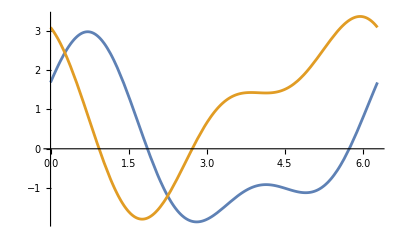

```mathematica
Plot[{Im[1+ⅇ^(2 ⅈ a′)+2 ⅇ^(ⅈ (1+a′))],Re[1+ⅇ^(2 ⅈ a′)+2 ⅇ^(ⅈ (1+a′))]},{a′,0,Pi 2}]
```

```mathematica
FunctionRange[1/4 (1+ⅇ^(2 ⅈ a′)+2 ⅇ^(ⅈ (1+a′))),a,w,Reals]
```

-1-ⅇ^(2 ⅈ a′)-2 ⅇ^(ⅈ (1+a′))+4 w==0

```mathematica
FunctionRange[{1/4 (1+ⅇ^(2 ⅈ a′ γ′)+2 ⅇ^(ⅈ (1+a′) γ′)),-Infinity<a′<Infinity&&0<=γ′<=Pi/2},{a,γ},w]//Reduce//FullSimplify
```

a′∈ℝ&&γ′≥0&&2 γ′≤π&&1+ⅇ^(2 ⅈ a′ γ′)+2 ⅇ^(ⅈ (1+a′) γ′)==4 w

```mathematica
a/.invsubs//ExpToTrig//Simplify
```

1/4 (1+Cos[2 a′ γ′]+2 Cos[γ′+a′ γ′]+ⅈ Sin[2 a′ γ′]+2 ⅈ Sin[γ′+a′ γ′])

```mathematica
subs = {γ′ ->1/2 I  Log[(-1+2 a-2 γ)/(a+γ)^2],
a′-> (-I  Log[2a-2γ-1])/(2 γ′)};
(J[a′,a′,γ′]//FullSimplify)//.subs//FullSimplify//MatrixForm
```

(a | 1/2 ⅈ (-1+a-γ) | 1/2 ⅈ (-1+a-γ) | γ
-1/2 ⅈ (-1+a-γ) | a | -γ | 1/2 ⅈ (-1+a-γ)
-1/2 ⅈ (-1+a-γ) | -γ | a | 1/2 ⅈ (-1+a-γ)
γ | -1/2 ⅈ (-1+a-γ) | -1/2 ⅈ (-1+a-γ) | a)

```mathematica
expressionWithF2=J[a′,a′,γ′][[1,1]]/. f->2;

FullSimplify[PowerExpand[expressionWithF2],Assumptions->a>0&&γ>0]
```

$Aborted

```mathematica
expressionWithF2=J[a′,a′,γ′][[1,1]]/. f->2;

(*Expand assuming a and Γ are real variables,then simplify*)
ComplexExpand[expressionWithF2,{a,γ}]//FullSimplify
```

$Aborted

```mathematica
J[1,1,1]
```

{{1/4 (1+3 ⅇ^(2 ⅈ)),1/4 ⅈ (-1+ⅇ^(2 ⅈ)),1/4 ⅈ (-1+ⅇ^(2 ⅈ)),1/4 (-1+ⅇ^(2 ⅈ))},{-1/4 ⅈ (-1+ⅇ^(2 ⅈ)),1/4 (1+3 ⅇ^(2 ⅈ)),1/4 (1-ⅇ^(2 ⅈ)),1/4 ⅈ (-1+ⅇ^(2 ⅈ))},{-1/4 ⅈ (-1+ⅇ^(2 ⅈ)),1/4 (1-ⅇ^(2 ⅈ)),1/4 (1+3 ⅇ^(2 ⅈ)),1/4 ⅈ (-1+ⅇ^(2 ⅈ))},{1/4 (-1+ⅇ^(2 ⅈ)),-1/4 ⅈ (-1+ⅇ^(2 ⅈ)),-1/4 ⅈ (-1+ⅇ^(2 ⅈ)),1/4 (1+3 ⅇ^(2 ⅈ))}}

```mathematica
J[aa,aa,g][[1,1]]//FullSimplify
```

1/4 ⅇ^(-ⅈ (1+aa) a′) (ⅇ^(ⅈ (1+aa) a′)+ⅇ^(ⅈ (1+aa) γ′)+ⅇ^(ⅈ (a′+aa a′+γ′))+ⅇ^(ⅈ (2 a′+aa γ′)))

```mathematica
ⅇ^(2 ⅈ Log[aa])
```

aa^(2 ⅈ)

```mathematica
(J[a,a,γ])//TrigToExp//Simplify//MatrixForm
```

(1/4 ⅇ^(-1/2 a′ (2 ⅈ+Log[a′]/(-a′+γ′))) (a′^(γ′/(2 (-a′+γ′))) ⅇ^(2 ⅈ a′)+a′^(a′/(2 (-a′+γ′))) ⅇ^(ⅈ (a′+γ′))+ⅇ^(1/2 a′ (2 ⅈ+Log[a′]/(-a′+γ′)))+ⅇ^(1/2 γ′ (2 ⅈ+Log[a′]/(-a′+γ′)))) | -1/4 ⅈ ⅇ^(-1/2 a′ (2 ⅈ+Log[a′]/(-a′+γ′))) (-a′^(γ′/(2 (-a′+γ′))) ⅇ^(2 ⅈ a′)-a′^(a′/(2 (-a′+γ′))) ⅇ^(ⅈ (a′+γ′))+ⅇ^(1/2 a′ (2 ⅈ+Log[a′]/(-a′+γ′)))+ⅇ^(1/2 γ′ (2 ⅈ+Log[a′]/(-a′+γ′)))) | 1/4 ⅈ ⅇ^(-1/2 a′ (2 ⅈ+Log[a′]/(-a′+γ′))) (a′^(γ′/(2 (-a′+γ′))) ⅇ^(2 ⅈ a′)-a′^(a′/(2 (-a′+γ′))) ⅇ^(ⅈ (a′+γ′))-ⅇ^(1/2 a′ (2 ⅈ+Log[a′]/(-a′+γ′)))+ⅇ^(1/2 γ′ (2 ⅈ+Log[a′]/(-a′+γ′)))) | 1/4 ⅇ^(-1/2 a′ (2 ⅈ+Log[a′]/(-a′+γ′))) (-a′^(γ′/(2 (-a′+γ′))) ⅇ^(2 ⅈ a′)+a′^(a′/(2 (-a′+γ′))) ⅇ^(ⅈ (a′+γ′))-ⅇ^(1/2 a′ (2 ⅈ+Log[a′]/(-a′+γ′)))+ⅇ^(1/2 γ′ (2 ⅈ+Log[a′]/(-a′+γ′))))
1/4 ⅈ ⅇ^(-1/2 a′ (2 ⅈ+Log[a′]/(-a′+γ′))) (-a′^(γ′/(2 (-a′+γ′))) ⅇ^(2 ⅈ a′)-a′^(a′/(2 (-a′+γ′))) ⅇ^(ⅈ (a′+γ′))+ⅇ^(1/2 a′ (2 ⅈ+Log[a′]/(-a′+γ′)))+ⅇ^(1/2 γ′ (2 ⅈ+Log[a′]/(-a′+γ′)))) | 1/4 ⅇ^(-1/2 a′ (2 ⅈ+Log[a′]/(-a′+γ′))) (a′^(γ′/(2 (-a′+γ′))) ⅇ^(2 ⅈ a′)+a′^(a′/(2 (-a′+γ′))) ⅇ^(ⅈ (a′+γ′))+ⅇ^(1/2 a′ (2 ⅈ+Log[a′]/(-a′+γ′)))+ⅇ^(1/2 γ′ (2 ⅈ+Log[a′]/(-a′+γ′)))) | 1/4 ⅇ^(-1/2 a′ (2 ⅈ+Log[a′]/(-a′+γ′))) (a′^(γ′/(2 (-a′+γ′))) ⅇ^(2 ⅈ a′)-a′^(a′/(2 (-a′+γ′))) ⅇ^(ⅈ (a′+γ′))+ⅇ^(1/2 a′ (2 ⅈ+Log[a′]/(-a′+γ′)))-ⅇ^(1/2 γ′ (2 ⅈ+Log[a′]/(-a′+γ′)))) | 1/4 ⅈ ⅇ^(-1/2 a′ (2 ⅈ+Log[a′]/(-a′+γ′))) (a′^(γ′/(2 (-a′+γ′))) ⅇ^(2 ⅈ a′)-a′^(a′/(2 (-a′+γ′))) ⅇ^(ⅈ (a′+γ′))-ⅇ^(1/2 a′ (2 ⅈ+Log[a′]/(-a′+γ′)))+ⅇ^(1/2 γ′ (2 ⅈ+Log[a′]/(-a′+γ′))))
1/4 ⅈ ⅇ^(-1/2 a′ (2 ⅈ+Log[a′]/(-a′+γ′))) (-a′^(γ′/(2 (-a′+γ′))) ⅇ^(2 ⅈ a′)+a′^(a′/(2 (-a′+γ′))) ⅇ^(ⅈ (a′+γ′))+ⅇ^(1/2 a′ (2 ⅈ+Log[a′]/(-a′+γ′)))-ⅇ^(1/2 γ′ (2 ⅈ+Log[a′]/(-a′+γ′)))) | 1/4 ⅇ^(-1/2 a′ (2 ⅈ+Log[a′]/(-a′+γ′))) (a′^(γ′/(2 (-a′+γ′))) ⅇ^(2 ⅈ a′)-a′^(a′/(2 (-a′+γ′))) ⅇ^(ⅈ (a′+γ′))+ⅇ^(1/2 a′ (2 ⅈ+Log[a′]/(-a′+γ′)))-ⅇ^(1/2 γ′ (2 ⅈ+Log[a′]/(-a′+γ′)))) | 1/4 ⅇ^(-1/2 a′ (2 ⅈ+Log[a′]/(-a′+γ′))) (a′^(γ′/(2 (-a′+γ′))) ⅇ^(2 ⅈ a′)+a′^(a′/(2 (-a′+γ′))) ⅇ^(ⅈ (a′+γ′))+ⅇ^(1/2 a′ (2 ⅈ+Log[a′]/(-a′+γ′)))+ⅇ^(1/2 γ′ (2 ⅈ+Log[a′]/(-a′+γ′)))) | -1/4 ⅈ ⅇ^(-1/2 a′ (2 ⅈ+Log[a′]/(-a′+γ′))) (-a′^(γ′/(2 (-a′+γ′))) ⅇ^(2 ⅈ a′)-a′^(a′/(2 (-a′+γ′))) ⅇ^(ⅈ (a′+γ′))+ⅇ^(1/2 a′ (2 ⅈ+Log[a′]/(-a′+γ′)))+ⅇ^(1/2 γ′ (2 ⅈ+Log[a′]/(-a′+γ′))))
1/4 ⅇ^(-1/2 a′ (2 ⅈ+Log[a′]/(-a′+γ′))) (-a′^(γ′/(2 (-a′+γ′))) ⅇ^(2 ⅈ a′)+a′^(a′/(2 (-a′+γ′))) ⅇ^(ⅈ (a′+γ′))-ⅇ^(1/2 a′ (2 ⅈ+Log[a′]/(-a′+γ′)))+ⅇ^(1/2 γ′ (2 ⅈ+Log[a′]/(-a′+γ′)))) | 1/4 ⅈ ⅇ^(-1/2 a′ (2 ⅈ+Log[a′]/(-a′+γ′))) (-a′^(γ′/(2 (-a′+γ′))) ⅇ^(2 ⅈ a′)+a′^(a′/(2 (-a′+γ′))) ⅇ^(ⅈ (a′+γ′))+ⅇ^(1/2 a′ (2 ⅈ+Log[a′]/(-a′+γ′)))-ⅇ^(1/2 γ′ (2 ⅈ+Log[a′]/(-a′+γ′)))) | 1/4 ⅈ ⅇ^(-1/2 a′ (2 ⅈ+Log[a′]/(-a′+γ′))) (-a′^(γ′/(2 (-a′+γ′))) ⅇ^(2 ⅈ a′)-a′^(a′/(2 (-a′+γ′))) ⅇ^(ⅈ (a′+γ′))+ⅇ^(1/2 a′ (2 ⅈ+Log[a′]/(-a′+γ′)))+ⅇ^(1/2 γ′ (2 ⅈ+Log[a′]/(-a′+γ′)))) | 1/4 ⅇ^(-1/2 a′ (2 ⅈ+Log[a′]/(-a′+γ′))) (a′^(γ′/(2 (-a′+γ′))) ⅇ^(2 ⅈ a′)+a′^(a′/(2 (-a′+γ′))) ⅇ^(ⅈ (a′+γ′))+ⅇ^(1/2 a′ (2 ⅈ+Log[a′]/(-a′+γ′)))+ⅇ^(1/2 γ′ (2 ⅈ+Log[a′]/(-a′+γ′)))))

```mathematica
symmetricJ = (J[a/γo,a/γo,γo])//FullSimplify;
```

```mathematica
symmetricJ = (symmetricJ/.γo->γ-a)//FullSimplify;
```

```mathematica
symmetricJ = ((symmetricJ//TrigToExp)/.{a->-I/2 Log[a],γ->-I Log[γ]});
```

```mathematica
((symmetricJ)4/.{a->a,γ->γ/2})//Simplify//MatrixForm
```

```mathematica
symmetricJ = (J[a′,a′,γ′]//FullSimplify)//.subs//FullSimplify;
```

```mathematica
finalStates = Table[play[symmetricJ,D4[[i]],D4[[j]]]//FullSimplify,{i,8},{j,8}]/.Conjugate->MyConj;
```

```mathematica
alicesScores = (Map[alicesScore,finalStates,{2}]/.Conjugate->MyConj)//FullSimplify;
bobsScores = (Map[bobsScore,finalStates,{2}]/.Conjugate->MyConj)//FullSimplify;
```

```mathematica
alicesScores//MatrixForm
```

(5 (a-γ)^2 (1-a+γ)^2+(2 a γ-1/2 (1-a+γ)^2)^2+3 (a^2+γ^2+1/2 (1-a+γ)^2)^2 | (a+γ)^2 (3 (a-γ)^2+5 (1-a+γ)^2) | 1/2 (1+20 a^4-2 a^3 (15+16 γ)+a^2 (19+42 γ+40 γ^2)-2 a (1+γ) (2+γ (5+16 γ))+γ (4+γ (19+10 γ (3+2 γ)))) | 1/2 (1+20 a^4-2 a^3 (15+16 γ)+a^2 (19+42 γ+40 γ^2)-2 a (1+γ) (2+γ (5+16 γ))+γ (4+γ (19+10 γ (3+2 γ)))) | 3/2 (a-γ)^2 (1-a+γ)^2+(1-a+γ)^2 (a^2+γ^2)+5/8 (a^2+(1+γ)^2-2 a (1+3 γ))^2 | 3/2 (a-γ)^2 (1-a+γ)^2+(1-a+γ)^2 (a^2+γ^2)+5/8 (a^2+(1+γ)^2-2 a (1+3 γ))^2 | (a-a^2+γ+γ^2)^2 | 4 (a-γ)^2 (1-a+γ)^2+5 (2 a γ-1/2 (1-a+γ)^2)^2
3 (a^2-γ^2)^2 | 3/4 (-1+a^2+(-2+γ) γ+2 a (1+γ))^2+(2 a γ+1/2 (1-a+γ)^2)^2 | 2 a^4+a^2 (3/2+γ)+a^3 (1+2 γ)+a (-2+γ) (1+γ) (1+2 γ)+1/2 (1+γ (4+γ (3-2 γ+4 γ^2))) | 2 a^4+a^2 (3/2+γ)+a^3 (1+2 γ)+a (-2+γ) (1+γ) (1+2 γ)+1/2 (1+γ (4+γ (3-2 γ+4 γ^2))) | 3/2 (1-a+γ)^2 (a+γ)^2+5/8 (a^2+2 a (-1+γ)+(1+γ)^2)^2 | 3/2 (1-a+γ)^2 (a+γ)^2+5/8 (4 a γ+(1-a+γ)^2)^2 | 5/4 (a^2+2 a (-1+γ)+(1+γ)^2)^2 | 3 (1-a+γ)^2 (a+γ)^2
1/2 (1+15 a^4-4 a^3 (5+8 γ)-4 a (1+γ) (1+γ (5+8 γ))+2 a^2 (7+γ (26+25 γ))+γ (4+γ (14+5 γ (4+3 γ)))) | 1/2 (1+9 a^4+4 a^3 (-2+γ)+4 a (1+γ) (-1+γ+γ^2)-2 a^2 (-4+γ (4+5 γ))+γ (4+γ (8+γ (8+9 γ)))) | 1+(13 a^4)/2-9 a^3 (1+γ)+a^2 (17/2+γ (17+5 γ))-a (1+γ) (4+γ (8+9 γ))+1/2 γ (8+γ (17+γ (18+13 γ))) | 4 a^2 γ^2+5/2 (1-a+γ)^2 (a^2+γ^2)+3 (a^2+γ^2)^2 | 5/4 (1-a+γ)^4+2 (1-a+γ)^2 (a^2+γ^2) | 20 a^2 γ^2+2 (1-a+γ)^2 (a^2+γ^2) | 1/2 (1-a+γ)^2 (a+γ)^2+5/8 (4 a γ+(1-a+γ)^2)^2 | 1/2 (a-γ)^2 (1-a+γ)^2+3 (1-a+γ)^2 (a^2+γ^2)+5/8 (a^2+(1+γ)^2-2 a (1+3 γ))^2
1/2 (1+15 a^4-4 a^3 (5+8 γ)-4 a (1+γ) (1+γ (5+8 γ))+2 a^2 (7+γ (26+25 γ))+γ (4+γ (14+5 γ (4+3 γ)))) | 1/2 (1+9 a^4+4 a^3 (-2+γ)+4 a (1+γ) (-1+γ+γ^2)-2 a^2 (-4+γ (4+5 γ))+γ (4+γ (8+γ (8+9 γ)))) | 4 a^2 γ^2+5/2 (1-a+γ)^2 (a^2+γ^2)+3 (a^2+γ^2)^2 | 1+(13 a^4)/2-9 a^3 (1+γ)+a^2 (17/2+γ (17+5 γ))-a (1+γ) (4+γ (8+9 γ))+1/2 γ (8+γ (17+γ (18+13 γ))) | 20 a^2 γ^2+2 (1-a+γ)^2 (a^2+γ^2) | 1/4 (1-a+γ)^2 (5+13 a^2-10 a (1+γ)+γ (10+13 γ)) | 1/2 (1-a+γ)^2 (a+γ)^2+5/8 (a^2+2 a (-1+γ)+(1+γ)^2)^2 | 1/8 (33 a^4-4 a^3 (19+31 γ)+a^2 (58+212 γ+262 γ^2)-4 a (1+γ) (5+γ (22+31 γ))+(1+γ)^2 (5+γ (10+33 γ)))
1/8 (5+85 a^4-4 a^3 (25+31 γ)-4 a (1+γ) (5+γ (16+31 γ))+2 a^2 (35+γ (94+79 γ))+5 γ (4+γ (14+γ (20+17 γ)))) | 3/2 (1-a+γ)^2 (a+γ)^2+5/8 (-1+(1+2 ⅈ) a^2+2 a (1+γ)+γ (-2+(1-2 ⅈ) γ)) (-1+(1-2 ⅈ) a^2+2 a (1+γ)+γ (-2+(1+2 ⅈ) γ)) | 2 (1-a+γ)^2 (a^2+γ^2)+5/4 (1+(1+2 ⅈ) a^2-2 a (1+γ)+γ (2+(1-2 ⅈ) γ)) (1+(1-2 ⅈ) a^2-2 a (1+γ)+γ (2+(1+2 ⅈ) γ)) | (a^2+γ^2) (2+7 a^2-4 a (1+γ)+γ (4+7 γ)) | 1/2 (2+9 a^4+8 γ-18 a^3 (1+γ)+γ^2 (17+9 γ (2+γ))-2 a (1+γ) (4+γ (8+9 γ))+a^2 (17+2 γ (17+9 γ))) | 12 a^2 γ^2+5/2 (1-a+γ)^2 (a^2+γ^2)+(a^2+γ^2)^2 | 1/2+a^4+2 γ+(5 γ^2)/2+γ^3+γ^4+a^3 (-1+2 γ)+a^2 (5/2+γ (-1+2 γ))+a (-2+γ (-3+γ+2 γ^2)) | 7 a^4-a^3 (13+16 γ)-a (1+γ) (2+γ (7+16 γ))+a^2 (17/2+γ (23+26 γ))+1/2 (1+γ (4+γ (17+2 γ (13+7 γ))))
1/8 (5+85 a^4-4 a^3 (25+31 γ)-4 a (1+γ) (5+γ (16+31 γ))+2 a^2 (35+γ (94+79 γ))+5 γ (4+γ (14+γ (20+17 γ)))) | 3/2 (1-a+γ)^2 (a+γ)^2+5/8 (-1+(1+2 ⅈ) a^2+2 a (1+γ)+γ (-2+(1-2 ⅈ) γ)) (-1+(1-2 ⅈ) a^2+2 a (1+γ)+γ (-2+(1+2 ⅈ) γ)) | (a^2+γ^2) (2+7 a^2-4 a (1+γ)+γ (4+7 γ)) | 1/4 (5+33 a^4-36 a^3 (1+γ)+a^2 (38+76 γ+6 γ^2)-4 a (1+γ) (5+γ (10+9 γ))+γ (20+γ (38+36 γ+33 γ^2))) | 12 a^2 γ^2+5/2 (1-a+γ)^2 (a^2+γ^2)+(a^2+γ^2)^2 | 1/2 (2+9 a^4+8 γ-18 a^3 (1+γ)+γ^2 (17+9 γ (2+γ))-2 a (1+γ) (4+γ (8+9 γ))+a^2 (17+2 γ (17+9 γ))) | 1/2+a^4+2 γ+(5 γ^2)/2+γ^3+γ^4+a^3 (-1+2 γ)+a^2 (5/2+γ (-1+2 γ))+a (-2+γ (-3+γ+2 γ^2)) | 7 a^4-a^3 (13+16 γ)-a (1+γ) (2+γ (7+16 γ))+a^2 (17/2+γ (23+26 γ))+1/2 (1+γ (4+γ (17+2 γ (13+7 γ))))
(a+γ)^2 (5 (a-γ)^2+(1-a+γ)^2) | 5/4 (-1+a^2+(-2+γ) γ+2 a (1+γ))^2 | 1/2 (1-a+γ)^2 (a+γ)^2+5/8 (-1+(1+2 ⅈ) a^2+2 a (1+γ)+γ (-2+(1-2 ⅈ) γ)) (-1+(1-2 ⅈ) a^2+2 a (1+γ)+γ (-2+(1+2 ⅈ) γ)) | 1/2 (1-a+γ)^2 (a+γ)^2+5/8 (-1+(1+2 ⅈ) a^2+2 a (1+γ)+γ (-2+(1-2 ⅈ) γ)) (-1+(1-2 ⅈ) a^2+2 a (1+γ)+γ (-2+(1+2 ⅈ) γ)) | 1/2+(7 a^4)/2+2 a^3 (-3+γ)+2 γ+5 γ^2+6 γ^3+(7 γ^4)/2+2 a (-1+γ+3 γ^2+γ^3)+a^2 (5-3 γ (2+γ)) | 1/2+(7 a^4)/2+2 a^3 (-3+γ)+2 γ+5 γ^2+6 γ^3+(7 γ^4)/2+2 a (-1+γ+3 γ^2+γ^3)+a^2 (5-3 γ (2+γ)) | (a^2+γ^2-1/2 (1-a+γ)^2)^2+3 (2 a γ+1/2 (1-a+γ)^2)^2 | 5 (1-a+γ)^2 (a+γ)^2+(a^2-γ^2)^2
4 (a-γ)^2 (1-a+γ)^2+5/4 (1+3 a^2-2 a (1+γ)+γ (2+3 γ))^2 | (a+γ)^2 (3+8 a^2+6 γ+8 γ^2-2 a (3+8 γ)) | 1/8 (5+93 a^4-4 a^3 (29+31 γ)-4 a (1+γ) (5+γ (12+31 γ))+2 a^2 (39+γ (86+71 γ))+γ (20+γ (78+γ (116+93 γ)))) | 1/8 (5+93 a^4-4 a^3 (29+31 γ)-4 a (1+γ) (5+γ (12+31 γ))+2 a^2 (39+γ (86+71 γ))+γ (20+γ (78+γ (116+93 γ)))) | 1/2+(9 a^4)/2+2 γ+6 γ^2+8 γ^3+(9 γ^4)/2-8 a^3 (1+2 γ)-2 a (1+γ) (1+2 γ) (1+4 γ)+a^2 (6+γ (28+31 γ)) | 1/2+(9 a^4)/2+2 γ+6 γ^2+8 γ^3+(9 γ^4)/2-8 a^3 (1+2 γ)-2 a (1+γ) (1+2 γ) (1+4 γ)+a^2 (6+γ (28+31 γ)) | (a^2-γ^2)^2 | 1+8 a^4-16 a^3 (1+2 γ)-4 a (1+γ) (1+2 γ) (1+4 γ)+4 a^2 (1+2 γ) (3+8 γ)+4 γ (1+γ) (1+2 γ (1+γ)))

```mathematica
bothScores =  Map[scores,finalStates,{2}]/.Conjugate->MyConj//FullSimplify;
```

```mathematica
DiscreteNashEquilibria[{{3,0},{5,1}},{{3,5},{0,1}}]
```

{{{2,2},{1,1},0<α≤π/2&&0<γ≤π/2}}

```mathematica
D4Sym[[{1,1}]]
```

{σ_0,σ_0}

```mathematica
eq = DiscreteNashEquilibria[(alicesScores),(bobsScores)];
```

$Aborted

```mathematica
eq//MatrixForm
```

```mathematica
equlibria = DeleteCases[eq/.{Reduce->id3},{_,_,False}];
```

```mathematica
equlibria//Length
```

29

```mathematica
equlibria = DeleteCases[Table[{D4Sym[[e[[1]]]],e[[2]],TimeConstrained[Reduce[FullSimplify[(e[[3]])]],3,e[[3]]]},{e,equlibria}],{_,_,False}]/.Reduce->Identity;
```

$Aborted

```mathematica
equlibria
```

```mathematica
Reduce[FullSimplify[equlibria[[1,3]],Assumptions->{0<b<=Pi/2}],{b,γ}]
```

$Aborted

```mathematica
equlibria = DeleteCases[Table[{D4Sym[[e[[1]]]],e[[2]],TimeConstrained[Reduce[FullSimplify[(e[[3]])&&0<γ<Pi/2&&0<b<Pi/2]],30,e[[3]]]},{e,equlibria}],{_,_,False}]/.Reduce->Identity;
```

```mathematica
fullConstraint=Or@@equlibria[[;;,3]];
```

```mathematica
equlibria[[;;,2,1]]
equlibria[[;;,3]]
```

```mathematica
equlibria[[1,3]]
```

Cos[2 α]+3 Cos[2 γ]≥0&&1+Cos[4 α]+6 Cos[2 γ]+7 Cos[2 (-1+α/γ) γ]+7 Cos[2 (1+α/γ) γ]≥6 Cos[2 α]&&Cos[4 α]+16 (3+2 Cos[2 α]) Cos[γ]^2+(6-14 Cos[2 α]) Cos[2 γ]+32 Sin[α] Sin[2 α] Sin[γ]+48 Sin[α]^2 Sin[γ]^2≥35+6 Cos[2 α]&&1+Cos[4 α]+18 Cos[2 γ]+7 Cos[2 (-1+α/γ) γ]+7 Cos[2 (1+α/γ) γ]-8 Sin[3 α-γ]+8 Sin[3 α+γ]≥2 (Cos[2 α]+8 Cos[α] Sin[γ])&&(3+2 Cos[2 α]) Cos[γ]^2+3 Sin[α]^2 Sin[γ] (2 Cos[α]+Sin[γ])≥5 Cos[α]^4+Sin[2 α]^2&&(3+2 Cos[2 α]) Cos[γ]^2+3 Sin[α]^2 Sin[γ]^2≥5 Cos[α]^4+Sin[2 α]^2+3 Sin[α] Sin[2 α] Sin[γ]&&(3+2 Cos[2 α]) Cos[γ]^2+3 Sin[α]^2 Sin[γ]^2≥5 Cos[α]^4+Sin[2 α]^2&&(3+Cos[2 α]) Cos[2 γ]+40 Cos[α]^2 Sin[γ]^2≥5+7 Cos[2 α]&&Cos[2 α] (-1+3 Cos[2 γ])≤0&&5 Cos[α]^2 Sin[γ]^2≥1+(-2+Cos[2 γ]) Sin[α]^2

```mathematica
equlibria[[1,3]]
```

Cos[2 α]+3 Cos[2 γ]≥0&&1+Cos[4 α]+6 Cos[2 γ]+7 Cos[2 (-1+α/γ) γ]+7 Cos[2 (1+α/γ) γ]≥6 Cos[2 α]&&Cos[4 α]+16 (3+2 Cos[2 α]) Cos[γ]^2+(6-14 Cos[2 α]) Cos[2 γ]+32 Sin[α] Sin[2 α] Sin[γ]+48 Sin[α]^2 Sin[γ]^2≥35+6 Cos[2 α]&&1+Cos[4 α]+18 Cos[2 γ]+7 Cos[2 (-1+α/γ) γ]+7 Cos[2 (1+α/γ) γ]-8 Sin[3 α-γ]+8 Sin[3 α+γ]≥2 (Cos[2 α]+8 Cos[α] Sin[γ])&&(3+2 Cos[2 α]) Cos[γ]^2+3 Sin[α]^2 Sin[γ] (2 Cos[α]+Sin[γ])≥5 Cos[α]^4+Sin[2 α]^2&&(3+2 Cos[2 α]) Cos[γ]^2+3 Sin[α]^2 Sin[γ]^2≥5 Cos[α]^4+Sin[2 α]^2+3 Sin[α] Sin[2 α] Sin[γ]&&(3+2 Cos[2 α]) Cos[γ]^2+3 Sin[α]^2 Sin[γ]^2≥5 Cos[α]^4+Sin[2 α]^2&&(3+Cos[2 α]) Cos[2 γ]+40 Cos[α]^2 Sin[γ]^2≥5+7 Cos[2 α]&&Cos[2 α] (-1+3 Cos[2 γ])≤0&&5 Cos[α]^2 Sin[γ]^2≥1+(-2+Cos[2 γ]) Sin[α]^2

Cos[2 α]+3 Cos[2 γ]≥0&&1+Cos[4 α]+6 Cos[2 γ]+7 Cos[2 (-1+α/γ) γ]+7 Cos[2 (1+α/γ) γ]≥6 Cos[2 α]&&Cos[4 α]+16 (3+2 Cos[2 α]) Cos[γ]^2+(6-14 Cos[2 α]) Cos[2 γ]+32 Sin[α] Sin[2 α] Sin[γ]+48 Sin[α]^2 Sin[γ]^2≥35+6 Cos[2 α]&&1+Cos[4 α]+18 Cos[2 γ]+7 Cos[2 (-1+α/γ) γ]+7 Cos[2 (1+α/γ) γ]-8 Sin[3 α-γ]+8 Sin[3 α+γ]≥2 (Cos[2 α]+8 Cos[α] Sin[γ])&&(3+2 Cos[2 α]) Cos[γ]^2+3 Sin[α]^2 Sin[γ] (2 Cos[α]+Sin[γ])≥5 Cos[α]^4+Sin[2 α]^2&&(3+2 Cos[2 α]) Cos[γ]^2+3 Sin[α]^2 Sin[γ]^2≥5 Cos[α]^4+Sin[2 α]^2+3 Sin[α] Sin[2 α] Sin[γ]&&(3+2 Cos[2 α]) Cos[γ]^2+3 Sin[α]^2 Sin[γ]^2≥5 Cos[α]^4+Sin[2 α]^2&&(3+Cos[2 α]) Cos[2 γ]+40 Cos[α]^2 Sin[γ]^2≥5+7 Cos[2 α]&&Cos[2 α] (-1+3 Cos[2 γ])≤0&&5 Cos[α]^2 Sin[γ]^2≥1+(-2+Cos[2 γ]) Sin[α]^2

```mathematica
Reduce[Simplify[equlibria[[5,3]]&&Pi/2>α>0&&Pi/2>γ>0]]
```

False

```mathematica
Manipulate[Evaluate[equlibria[[5,3]]],{α,0,Pi/2},{γ,0,Pi/2}]
```

```mathematica
DensityPlot[equlibria[[5,2,1]],{α,10^-5, Pi/2},{γ,10^-5,Pi/2},RegionFunction->Function[{α,γ},Evaluate[equlibria[[5,3]]]]]//Quiet
```

-Graphics-

```mathematica
Table[DensityPlot[equlibria[[i,2,1]],{α,0, Pi/2},{γ,0,Pi/2},RegionFunction->Function[{α,γ},Evaluate[equlibria[[i,3]]]]]//Quiet,{i,12}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

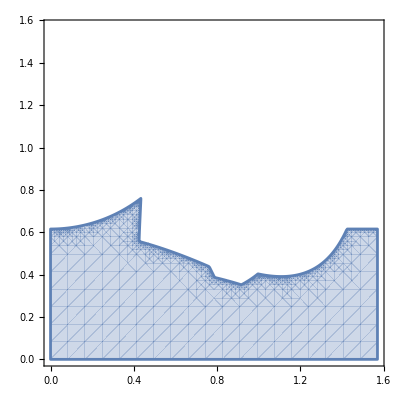

```mathematica
RegionPlot[fullConstraint,{α,0,Pi/2},{γ,0,Pi/2},MaxRecursion->6]
```

```mathematica
equlibria//MatrixForm
```

({σ_z,σ_y} | {Cos[γ]^2 (3+2 Cos[2 a γ])+3 Sin[γ]^2 Sin[a γ]^2,5 Cos[a γ]^2 Sin[γ]^2-(-2+Cos[2 γ]) Sin[a γ]^2} | 3 Cos[2 γ]+Cos[2 a γ]≥0&&1+6 Cos[2 γ]+7 Cos[2 (-1+a) γ]+Cos[4 a γ]+7 Cos[2 (1+a) γ]≥6 Cos[2 a γ]&&Cos[2 γ] (6-14 Cos[2 a γ])+16 Cos[γ]^2 (3+2 Cos[2 a γ])+Cos[4 a γ]+48 Sin[γ]^2 Sin[a γ]^2+32 Sin[γ] Sin[a γ] Sin[2 a γ]≥35+6 Cos[2 a γ]&&1+18 Cos[2 γ]+7 Cos[2 (-1+a) γ]+Cos[4 a γ]+7 Cos[2 (1+a) γ]+8 Sin[γ-3 a γ]+8 Sin[γ+3 a γ]≥2 (Cos[2 a γ]+8 Cos[a γ] Sin[γ])&&Cos[γ]^2 (3+2 Cos[2 a γ])+3 Sin[γ] (2 Cos[a γ]+Sin[γ]) Sin[a γ]^2≥5 Cos[a γ]^4+Sin[2 a γ]^2&&Cos[γ]^2 (3+2 Cos[2 a γ])+3 Sin[γ]^2 Sin[a γ]^2≥5 Cos[a γ]^4+3 Sin[γ] Sin[a γ] Sin[2 a γ]+Sin[2 a γ]^2&&Cos[γ]^2 (3+2 Cos[2 a γ])+3 Sin[γ]^2 Sin[a γ]^2≥5 Cos[a γ]^4+Sin[2 a γ]^2&&Cos[2 γ] (3+Cos[2 a γ])+40 Cos[a γ]^2 Sin[γ]^2≥5+7 Cos[2 a γ]&&(-1+3 Cos[2 γ]) Cos[2 a γ]≤0&&5 Cos[a γ]^2 Sin[γ]^2≥1+(-2+Cos[2 γ]) Sin[a γ]^2
{Sσ_x,Sσ_x} | {1/32 (69-16 Cos[2 γ]-8 Cos[2 (-1+a) γ]-4 Cos[2 a γ]-Cos[4 a γ]-8 Cos[2 (1+a) γ]+8 Sin[γ] Sin[a γ] Sin[2 a γ]),1/32 (69-16 Cos[2 γ]-8 Cos[2 (-1+a) γ]-4 Cos[2 a γ]-Cos[4 a γ]-8 Cos[2 (1+a) γ]+8 Sin[γ] Sin[a γ] Sin[2 a γ])} | 17+8 Sin[γ] Sin[a γ] Sin[2 a γ]≥8 Cos[2 (-1+a) γ]+Cos[4 a γ]+8 Cos[2 (1+a) γ]+56 Cos[2 γ] Sin[a γ]^2&&8 Cos[2 γ]+4 Cos[2 (-1+a) γ]+Cos[4 a γ]+4 Cos[2 (1+a) γ]+3 Sin[γ-3 a γ]+3 Sin[γ+3 a γ]≤17+16 Cos[2 a γ]+6 Cos[a γ] Sin[γ]&&69+8 Cos[2 γ] (-3+Cos[2 a γ])+8 Sin[γ] Sin[a γ] Sin[2 a γ]≥8 Cos[2 (-1+a) γ]+4 Cos[2 a γ]+Cos[4 a γ]+8 Cos[2 (1+a) γ]+80 Cos[a γ]^2 Sin[γ]^2+32 Sin[a γ]^2&&2+2 Cos[2 a γ]+6 Sin[γ] Sin[a γ] Sin[2 a γ]≥2 Cos[2 γ]+Cos[2 (-1+a) γ]+Cos[2 (1+a) γ]&&16 Cos[2 a γ]+Cos[4 a γ]+8 Sin[a γ] (3 Cos[2 γ] Sin[a γ]+5 Sin[γ] Sin[2 a γ])≥1+8 Cos[2 (-1+a) γ]+8 Cos[2 (1+a) γ]&&24 Cos[2 γ] Cos[a γ]^2+32 Cos[2 a γ]≥5+8 Cos[2 (-1+a) γ]+3 Cos[4 a γ]+8 Cos[2 (1+a) γ]+24 Sin[γ] Sin[a γ] Sin[2 a γ]&&6 (2 Cos[2 γ]+Cos[2 (-1+a) γ]+Cos[2 (1+a) γ])≥3+4 Cos[2 a γ]+Cos[4 a γ]+20 Sin[γ] Sin[a γ] Sin[2 a γ]
{Sσ_x,σ_y} | {1/8 (13+3 Cos[2 γ]-(1+7 Cos[2 γ]) Cos[2 a γ]),1/8 (13-7 Cos[2 γ]+(-1+3 Cos[2 γ]) Cos[2 a γ])} | 2+3 Cos[2 γ]≥Cos[2 a γ]&&Cos[2 γ] (20-8 Cos[2 a γ])+16 Cos[2 a γ]≥11+Cos[4 a γ]+16 Sin[γ] Sin[a γ] Sin[2 a γ]&&Cos[2 γ] (52-28 Cos[2 a γ])+20 (Cos[2 (-1+a) γ]+Cos[2 (1+a) γ])≥23+8 Cos[2 a γ]+Cos[4 a γ]+48 Sin[γ] Sin[a γ] Sin[2 a γ]&&17+32 Cos[2 a γ]+16 Sin[γ] Sin[a γ] Sin[2 a γ]≥4 Cos[2 γ] (-3+7 Cos[2 a γ])+Cos[4 a γ]&&8 Cos[2 (-1+a) γ]+Cos[4 a γ]+8 Cos[2 (1+a) γ]+56 Cos[2 γ] Sin[a γ]^2≥17+8 Sin[γ] Sin[a γ] Sin[2 a γ]&&16 Cos[2 a γ]+Cos[4 a γ]+40 Sin[γ] Sin[a γ] Sin[2 a γ]≥1+4 Cos[2 γ] (-3+7 Cos[2 a γ])&&Sin[a γ]^2 (-5+10 Cos[2 γ]-Cos[a γ]^2+8 Cos[a γ] Sin[γ]+Sin[a γ]^2)≥0&&5+7 Cos[2 a γ]≥Cos[2 γ] (3+Cos[2 a γ])+40 Cos[a γ]^2 Sin[γ]^2&&18+Cos[2 (-1+a) γ]+6 Cos[2 a γ]+Cos[2 (1+a) γ]≥10 (Cos[2 γ]+4 Cos[a γ]^2 Sin[γ]^2)&&2 (7 Cos[2 γ]+Cos[2 a γ])≥10+3 Cos[2 (-1+a) γ]+3 Cos[2 (1+a) γ]&&5+Cos[2 γ] (-7+3 Cos[2 a γ])≥Cos[2 a γ]
{Sσ_y,Sσ_y} | {1/32 (69-16 Cos[2 γ]-8 Cos[2 (-1+a) γ]-4 Cos[2 a γ]-Cos[4 a γ]-8 Cos[2 (1+a) γ]-8 Sin[γ] Sin[a γ] Sin[2 a γ]),1/32 (69-16 Cos[2 γ]-8 Cos[2 (-1+a) γ]-4 Cos[2 a γ]-Cos[4 a γ]-8 Cos[2 (1+a) γ]-8 Sin[γ] Sin[a γ] Sin[2 a γ])} | 8 Cos[2 (-1+a) γ]+Cos[4 a γ]+8 (Cos[2 (1+a) γ]+7 Cos[2 γ] Sin[a γ]^2+Sin[γ] Sin[a γ] Sin[2 a γ])≤17&&8 Cos[2 γ]+4 Cos[2 (-1+a) γ]+Cos[4 a γ]+4 Cos[2 (1+a) γ]+3 Sin[γ-a γ]+3 Sin[γ+a γ]≤17+16 Cos[2 a γ]+3 Sin[γ-3 a γ]+3 Sin[γ+3 a γ]&&69+8 Cos[2 γ] (-3+Cos[2 a γ])≥8 Cos[2 (-1+a) γ]+4 Cos[2 a γ]+Cos[4 a γ]+8 Cos[2 (1+a) γ]+80 Cos[a γ]^2 Sin[γ]^2+32 Sin[a γ]^2+8 Sin[γ] Sin[a γ] Sin[2 a γ]&&12 Cos[2 γ]+16 Cos[2 a γ]+Cos[4 a γ]+10 Sin[γ-3 a γ]+10 Sin[γ+3 a γ]≥1+14 Cos[2 (-1+a) γ]+14 Cos[2 (1+a) γ]+20 Cos[a γ] Sin[γ]&&6 Cos[2 γ]+3 Cos[2 (-1+a) γ]+3 Cos[2 (1+a) γ]+10 Sin[γ] Sin[a γ] Sin[2 a γ]≥4 Cos[a γ]^4&&8 (3 Cos[2 γ] Cos[a γ]^2+4 Cos[2 a γ]+3 Sin[γ] Sin[a γ] Sin[2 a γ])≥5+8 Cos[2 (-1+a) γ]+3 Cos[4 a γ]+8 Cos[2 (1+a) γ]&&4 Cos[a γ]^2≥2 Cos[2 γ]+Cos[2 (-1+a) γ]+Cos[2 (1+a) γ]+6 Sin[γ] Sin[a γ] Sin[2 a γ]
{Sσ_y,σ_y} | {1/8 (13+3 Cos[2 γ]-(1+7 Cos[2 γ]) Cos[2 a γ]),1/8 (13-7 Cos[2 γ]+(-1+3 Cos[2 γ]) Cos[2 a γ])} | 2+3 Cos[2 γ]≥Cos[2 a γ]&&Cos[2 γ] (20-8 Cos[2 a γ])+16 (Cos[2 a γ]+Sin[γ] Sin[a γ] Sin[2 a γ])≥11+Cos[4 a γ]&&13+Cos[2 γ] (3-7 Cos[2 a γ])≥Cos[a γ]^2 Cos[2 a γ]+17 Sin[a γ]^2+4 Sin[γ] Sin[a γ] Sin[2 a γ]&&20 Cos[2 (-1+a) γ]+Cos[2 γ] (52-28 Cos[2 a γ])+20 Cos[2 (1+a) γ]+48 Sin[γ] Sin[a γ] Sin[2 a γ]≥23+8 Cos[2 a γ]+Cos[4 a γ]&&16 Cos[2 a γ]+Cos[4 a γ]≥1+4 Cos[2 γ] (-3+7 Cos[2 a γ])+40 Sin[γ] Sin[a γ] Sin[2 a γ]&&8 Cos[2 (-1+a) γ]+Cos[4 a γ]+8 (Cos[2 (1+a) γ]+7 Cos[2 γ] Sin[a γ]^2+Sin[γ] Sin[a γ] Sin[2 a γ])≥17&&Cos[2 γ] (20-14 Cos[2 a γ])+8 Cos[2 a γ]+Cos[4 a γ]+4 Sin[γ-3 a γ]+4 Sin[γ+3 a γ]≥9+3 Cos[2 (-1+a) γ]+3 Cos[2 (1+a) γ]+8 Cos[a γ] Sin[γ]&&5+7 Cos[2 a γ]≥Cos[2 γ] (3+Cos[2 a γ])+40 Cos[a γ]^2 Sin[γ]^2&&18+Cos[2 (-1+a) γ]+6 Cos[2 a γ]+Cos[2 (1+a) γ]≥10 (Cos[2 γ]+4 Cos[a γ]^2 Sin[γ]^2)&&2 (7 Cos[2 γ]+Cos[2 a γ])≥10+3 Cos[2 (-1+a) γ]+3 Cos[2 (1+a) γ]&&5+Cos[2 γ] (-7+3 Cos[2 a γ])≥Cos[2 a γ]
{σ_x,σ_y} | {Cos[γ]^2 (3-2 Cos[2 a γ])+3 Cos[a γ]^2 Sin[γ]^2,Cos[γ]^2 Cos[a γ]^2-(-4+Cos[2 a γ]) Sin[γ]^2} | 3 Cos[2 γ]≥Cos[2 a γ]&&Cos[γ]^2 (3-2 Cos[2 a γ])+3 Cos[a γ]^2 Sin[γ]^2≥5 Sin[a γ]^4+Sin[2 a γ]^2&&18 Cos[2 γ]+14 Cos[2 a γ]≥1+7 Cos[2 (-1+a) γ]+Cos[4 a γ]+7 Cos[2 (1+a) γ]+32 Sin[γ] Sin[a γ] Sin[2 a γ]&&Cos[γ]^2 (3-2 Cos[2 a γ])+3 Cos[a γ]^2 Sin[γ]^2≥1/8 (5 (-1+Cos[2 a γ]+2 Cos[a γ] Sin[γ])^2+6 (2+Cos[2 γ]+Cos[2 a γ]) Sin[a γ]^2+4 (Cos[a γ]+Sin[γ])^2 Sin[a γ]^2)&&7 Cos[2 (-1+a) γ]+Cos[γ]^2 (48-32 Cos[2 a γ])+10 Cos[2 a γ]+Cos[4 a γ]+7 Cos[2 (1+a) γ]+48 Cos[a γ]^2 Sin[γ]^2≥35+6 Cos[2 γ]+24 Sin[γ] Sin[a γ] Sin[2 a γ]&&Cos[γ]^2 (48-32 Cos[2 a γ])+10 Cos[2 a γ]+2 Cos[2 γ] (-3+7 Cos[2 a γ])+Cos[4 a γ]+48 Cos[a γ]^2 Sin[γ]^2+24 Sin[γ] Sin[a γ] Sin[2 a γ]≥35&&1+6 Cos[2 γ]+6 Cos[2 a γ]+Cos[4 a γ]≥7 (Cos[2 (-1+a) γ]+Cos[2 (1+a) γ])&&(-1+3 Cos[2 γ]) Cos[2 a γ]≥0&&9 (2+Cos[2 (-1+a) γ]+Cos[2 (1+a) γ])≥14 Cos[2 γ]+6 Cos[2 a γ]&&10+3 Cos[2 (-1+a) γ]+3 Cos[2 (1+a) γ]≥2 (7 Cos[2 γ]+Cos[2 a γ])&&Cos[γ]^2 Cos[a γ]^2≥1+(-4+Cos[2 a γ]) Sin[γ]^2
{σ_y,σ_z} | {5 Cos[a γ]^2 Sin[γ]^2-(-2+Cos[2 γ]) Sin[a γ]^2,Cos[γ]^2 (3+2 Cos[2 a γ])+3 Sin[γ]^2 Sin[a γ]^2} | Cos[2 γ] (3+Cos[2 a γ])+40 Cos[a γ]^2 Sin[γ]^2≥5+7 Cos[2 a γ]&&(-1+3 Cos[2 γ]) Cos[2 a γ]≤0&&5 Cos[a γ]^2 Sin[γ]^2≥1+(-2+Cos[2 γ]) Sin[a γ]^2&&3 Cos[2 γ]+Cos[2 a γ]≥0&&1+6 Cos[2 γ]+7 Cos[2 (-1+a) γ]+Cos[4 a γ]+7 Cos[2 (1+a) γ]≥6 Cos[2 a γ]&&Cos[2 γ] (6-14 Cos[2 a γ])+16 Cos[γ]^2 (3+2 Cos[2 a γ])+Cos[4 a γ]+48 Sin[γ]^2 Sin[a γ]^2+32 Sin[γ] Sin[a γ] Sin[2 a γ]≥35+6 Cos[2 a γ]&&1+18 Cos[2 γ]+7 Cos[2 (-1+a) γ]+Cos[4 a γ]+7 Cos[2 (1+a) γ]+8 Sin[γ-3 a γ]+8 Sin[γ+3 a γ]≥2 (Cos[2 a γ]+8 Cos[a γ] Sin[γ])&&Cos[γ]^2 (3+2 Cos[2 a γ])+3 Sin[γ] (2 Cos[a γ]+Sin[γ]) Sin[a γ]^2≥5 Cos[a γ]^4+Sin[2 a γ]^2&&Cos[γ]^2 (3+2 Cos[2 a γ])+3 Sin[γ]^2 Sin[a γ]^2≥5 Cos[a γ]^4+3 Sin[γ] Sin[a γ] Sin[2 a γ]+Sin[2 a γ]^2&&Cos[γ]^2 (3+2 Cos[2 a γ])+3 Sin[γ]^2 Sin[a γ]^2≥5 Cos[a γ]^4+Sin[2 a γ]^2
{σ_y,Sσ_x} | {1/8 (13-7 Cos[2 γ]+(-1+3 Cos[2 γ]) Cos[2 a γ]),1/8 (13+3 Cos[2 γ]-(1+7 Cos[2 γ]) Cos[2 a γ])} | 5+7 Cos[2 a γ]≥Cos[2 γ] (3+Cos[2 a γ])+40 Cos[a γ]^2 Sin[γ]^2&&18+Cos[2 (-1+a) γ]+6 Cos[2 a γ]+Cos[2 (1+a) γ]≥10 (Cos[2 γ]+4 Cos[a γ]^2 Sin[γ]^2)&&2 (7 Cos[2 γ]+Cos[2 a γ])≥10+3 Cos[2 (-1+a) γ]+3 Cos[2 (1+a) γ]&&5+Cos[2 γ] (-7+3 Cos[2 a γ])≥Cos[2 a γ]&&2+3 Cos[2 γ]≥Cos[2 a γ]&&Cos[2 γ] (20-8 Cos[2 a γ])+16 Cos[2 a γ]≥11+Cos[4 a γ]+16 Sin[γ] Sin[a γ] Sin[2 a γ]&&Cos[2 γ] (52-28 Cos[2 a γ])+20 (Cos[2 (-1+a) γ]+Cos[2 (1+a) γ])≥23+8 Cos[2 a γ]+Cos[4 a γ]+48 Sin[γ] Sin[a γ] Sin[2 a γ]&&17+32 Cos[2 a γ]+16 Sin[γ] Sin[a γ] Sin[2 a γ]≥4 Cos[2 γ] (-3+7 Cos[2 a γ])+Cos[4 a γ]&&8 Cos[2 (-1+a) γ]+Cos[4 a γ]+8 Cos[2 (1+a) γ]+56 Cos[2 γ] Sin[a γ]^2≥17+8 Sin[γ] Sin[a γ] Sin[2 a γ]&&16 Cos[2 a γ]+Cos[4 a γ]+40 Sin[γ] Sin[a γ] Sin[2 a γ]≥1+4 Cos[2 γ] (-3+7 Cos[2 a γ])&&Sin[a γ]^2 (-5+10 Cos[2 γ]-Cos[a γ]^2+8 Cos[a γ] Sin[γ]+Sin[a γ]^2)≥0
{σ_y,Sσ_y} | {1/8 (13-7 Cos[2 γ]+(-1+3 Cos[2 γ]) Cos[2 a γ]),1/8 (13+3 Cos[2 γ]-(1+7 Cos[2 γ]) Cos[2 a γ])} | 5+7 Cos[2 a γ]≥Cos[2 γ] (3+Cos[2 a γ])+40 Cos[a γ]^2 Sin[γ]^2&&18+Cos[2 (-1+a) γ]+6 Cos[2 a γ]+Cos[2 (1+a) γ]≥10 (Cos[2 γ]+4 Cos[a γ]^2 Sin[γ]^2)&&2 (7 Cos[2 γ]+Cos[2 a γ])≥10+3 Cos[2 (-1+a) γ]+3 Cos[2 (1+a) γ]&&5+Cos[2 γ] (-7+3 Cos[2 a γ])≥Cos[2 a γ]&&2+3 Cos[2 γ]≥Cos[2 a γ]&&Cos[2 γ] (20-8 Cos[2 a γ])+16 (Cos[2 a γ]+Sin[γ] Sin[a γ] Sin[2 a γ])≥11+Cos[4 a γ]&&13+Cos[2 γ] (3-7 Cos[2 a γ])≥Cos[a γ]^2 Cos[2 a γ]+17 Sin[a γ]^2+4 Sin[γ] Sin[a γ] Sin[2 a γ]&&20 Cos[2 (-1+a) γ]+Cos[2 γ] (52-28 Cos[2 a γ])+20 Cos[2 (1+a) γ]+48 Sin[γ] Sin[a γ] Sin[2 a γ]≥23+8 Cos[2 a γ]+Cos[4 a γ]&&16 Cos[2 a γ]+Cos[4 a γ]≥1+4 Cos[2 γ] (-3+7 Cos[2 a γ])+40 Sin[γ] Sin[a γ] Sin[2 a γ]&&8 Cos[2 (-1+a) γ]+Cos[4 a γ]+8 (Cos[2 (1+a) γ]+7 Cos[2 γ] Sin[a γ]^2+Sin[γ] Sin[a γ] Sin[2 a γ])≥17&&Cos[2 γ] (20-14 Cos[2 a γ])+8 Cos[2 a γ]+Cos[4 a γ]+4 Sin[γ-3 a γ]+4 Sin[γ+3 a γ]≥9+3 Cos[2 (-1+a) γ]+3 Cos[2 (1+a) γ]+8 Cos[a γ] Sin[γ]
{σ_y,σ_x} | {Cos[γ]^2 Cos[a γ]^2-(-4+Cos[2 a γ]) Sin[γ]^2,Cos[γ]^2 (3-2 Cos[2 a γ])+3 Cos[a γ]^2 Sin[γ]^2} | (-1+3 Cos[2 γ]) Cos[2 a γ]≥0&&9 (2+Cos[2 (-1+a) γ]+Cos[2 (1+a) γ])≥14 Cos[2 γ]+6 Cos[2 a γ]&&10+3 Cos[2 (-1+a) γ]+3 Cos[2 (1+a) γ]≥2 (7 Cos[2 γ]+Cos[2 a γ])&&Cos[γ]^2 Cos[a γ]^2≥1+(-4+Cos[2 a γ]) Sin[γ]^2&&3 Cos[2 γ]≥Cos[2 a γ]&&Cos[γ]^2 (3-2 Cos[2 a γ])+3 Cos[a γ]^2 Sin[γ]^2≥5 Sin[a γ]^4+Sin[2 a γ]^2&&18 Cos[2 γ]+14 Cos[2 a γ]≥1+7 Cos[2 (-1+a) γ]+Cos[4 a γ]+7 Cos[2 (1+a) γ]+32 Sin[γ] Sin[a γ] Sin[2 a γ]&&Cos[γ]^2 (3-2 Cos[2 a γ])+3 Cos[a γ]^2 Sin[γ]^2≥1/8 (5 (-1+Cos[2 a γ]+2 Cos[a γ] Sin[γ])^2+6 (2+Cos[2 γ]+Cos[2 a γ]) Sin[a γ]^2+4 (Cos[a γ]+Sin[γ])^2 Sin[a γ]^2)&&7 Cos[2 (-1+a) γ]+Cos[γ]^2 (48-32 Cos[2 a γ])+10 Cos[2 a γ]+Cos[4 a γ]+7 Cos[2 (1+a) γ]+48 Cos[a γ]^2 Sin[γ]^2≥35+6 Cos[2 γ]+24 Sin[γ] Sin[a γ] Sin[2 a γ]&&Cos[γ]^2 (48-32 Cos[2 a γ])+10 Cos[2 a γ]+2 Cos[2 γ] (-3+7 Cos[2 a γ])+Cos[4 a γ]+48 Cos[a γ]^2 Sin[γ]^2+24 Sin[γ] Sin[a γ] Sin[2 a γ]≥35&&1+6 Cos[2 γ]+6 Cos[2 a γ]+Cos[4 a γ]≥7 (Cos[2 (-1+a) γ]+Cos[2 (1+a) γ])
{σ_y,σ_y} | {1,1} | 5+Cos[2 γ] (-7+3 Cos[2 a γ])≤Cos[2 a γ]&&Cos[γ]^2 Cos[a γ]^2≤1+(-4+Cos[2 a γ]) Sin[γ]^2&&5 Cos[a γ]^2 Sin[γ]^2≤1+(-2+Cos[2 γ]) Sin[a γ]^2)

```mathematica
fullConstraint=Xor@@equlibria[[;;,3]];
fullConstraint = fullConstraint//Simplify;
```

```mathematica
Reduce[fullConstraint,{a,γ}]
```

$Aborted

```mathematica
Manipulate[DeleteCases[equlibria/.{a->A,γ->g},{_,_,False}]//MatrixForm,{A,0,10},{{g,2 ArcTan[√(5-2 √6)]+10^-2},0,Pi/2}]
```

```mathematica
Reduce[eq[[1,3]]]
```

((C[1]|C[2])∈ℤ&&C[1]≥0&&C[2]≥1&&γ==((2+4 C[1]) (-π+4 π C[2]))/(2 (-1+4 C[2]))&&a==(-1+4 C[2])/(2+4 C[1]))||((C[1]|C[2])∈ℤ&&C[1]≥0&&C[2]≥0&&γ==((2+4 C[1]) (π+4 π C[2]))/(2 (1+4 C[2]))&&a==(1+4 C[2])/(2+4 C[1]))||((C[1]|C[2])∈ℤ&&C[1]≥1&&C[2]≥1&&γ==2 π C[1]&&a==(-1+4 C[2])/(4 C[1]))||((C[1]|C[2])∈ℤ&&C[2]≥0&&C[1]≥1&&γ==2 π C[1]&&a==(1+4 C[2])/(4 C[1]))||((C[1]|C[2])∈ℤ&&C[2]≤0&&C[1]≤-1&&γ==((2+4 C[1]) (-π+4 π C[2]))/(2 (-1+4 C[2]))&&a==(-1+4 C[2])/(2+4 C[1]))||((C[1]|C[2])∈ℤ&&C[2]≤0&&C[1]≤-1&&γ==2 π C[1]&&a==(-1+4 C[2])/(4 C[1]))||((C[1]|C[2])∈ℤ&&C[1]≤-1&&C[2]≤-1&&γ==((2+4 C[1]) (π+4 π C[2]))/(2 (1+4 C[2]))&&a==(1+4 C[2])/(2+4 C[1]))||((C[1]|C[2])∈ℤ&&C[1]≤-1&&C[2]≤-1&&γ==2 π C[1]&&a==(1+4 C[2])/(4 C[1]))

```mathematica
id3[x_,_,_]:=x
```

```mathematica
eq/.Reduce->id3
```

{{{4,4},{17/8+Cos[2 a γ]-1/8 Cos[4 a γ],17/8+Cos[2 a γ]-1/8 Cos[4 a γ]},(C[1]|C[2])∈ℤ&&((((C[1]≤-1&&C[2]≤0&&a==(-1+4 C[2])/(2+4 C[1]))||(C[1]≥0&&C[2]≥1&&a==(-1+4 C[2])/(2+4 C[1])))&&γ==-(π-4 π C[2])/(2 a))||(((C[1]≤-1&&C[2]≤-1&&a==(1+4 C[2])/(2+4 C[1]))||(C[1]≥0&&C[2]≥0&&a==(1+4 C[2])/(2+4 C[1])))&&γ==-(-π-4 π C[2])/(2 a))||(C[1]≤-1&&((C[2]≤0&&a==-(π-4 π C[2])/(4 π C[1])&&γ==2 π C[1])||(C[2]≤-1&&a==-(-π-4 π C[2])/(4 π C[1])&&γ==2 π C[1])))||(C[1]≥1&&((C[2]≥1&&a==-(π-4 π C[2])/(4 π C[1])&&γ==2 π C[1])||(C[2]≥0&&a==-(-π-4 π C[2])/(4 π C[1])&&γ==2 π C[1]))))},{{4,8},{Cos[γ]^2 (3+2 Cos[2 a γ])+3 Sin[γ]^2 Sin[a γ]^2,5 Cos[a γ]^2 Sin[γ]^2-(-2+Cos[2 γ]) Sin[a γ]^2},1+2 Cos[2 γ] (9+14 Cos[2 a γ])+Cos[4 a γ]≥7 Cos[2 (-1+a) γ]+2 Cos[2 a γ]+7 Cos[2 (1+a) γ]+32 Sin[γ] Sin[a γ] Sin[2 a γ]&&1+2 Cos[2 γ] (9+7 Cos[2 a γ])+Cos[4 a γ]+32 Sin[γ] Sin[a γ] Sin[2 a γ]≥2 Cos[2 a γ]&&1+6 Cos[2 γ]+7 Cos[2 (-1+a) γ]+Cos[4 a γ]+7 Cos[2 (1+a) γ]≥6 Cos[2 a γ]&&Cos[2 γ] (3+7 Cos[2 a γ])≥Cos[2 a γ] (9+Cos[2 a γ])&&Cos[2 γ] (6+28 Cos[2 a γ])≥1+7 Cos[2 (-1+a) γ]+18 Cos[2 a γ]+Cos[4 a γ]+7 Cos[2 (1+a) γ]+24 Sin[γ] Sin[a γ] Sin[2 a γ]&&Cos[γ]^2 (3+2 Cos[2 a γ])+3 Sin[γ] (2 Cos[a γ]+Sin[γ]) Sin[a γ]^2≥5 Cos[a γ]^4+Sin[2 a γ]^2&&(-1+3 Cos[2 γ]) Cos[2 a γ]≤0&&5+3 Cos[2 a γ]≥Cos[2 γ] (7+9 Cos[2 a γ])&&5 Cos[a γ]^2 Sin[γ]^2≥1+(-2+Cos[2 γ]) Sin[a γ]^2&&a≥0},{{5,5},{1/8 (17-8 Cos[2 a γ]-Cos[4 a γ]),1/8 (17-8 Cos[2 a γ]-Cos[4 a γ])},((C[1]|C[2])∈ℤ&&((C[2]≤-1&&C[1]≤-1&&a==(π+2 π C[2])/(π+2 π C[1])&&γ==π+2 π C[1])||(C[2]≥0&&C[1]≥0&&a==(π+2 π C[2])/(π+2 π C[1])&&γ==π+2 π C[1])||(C[1]≤-1&&((C[2]≤-1&&a==(π+2 π C[1])/(2 π C[2])&&γ==2 π C[2])||(C[2]≤0&&a==C[2]/C[1]&&γ==2 π C[1])))||(C[1]≥0&&C[2]≥1&&a==(π+2 π C[1])/(2 π C[2])&&γ==2 π C[2])||(((C[1]≤-1&&C[2]≤-1&&a==(2 C[2])/(1+2 C[1]))||(C[1]≥0&&C[2]≥1&&a==(2 C[2])/(1+2 C[1])))&&γ==(2 π C[2])/a)||(C[1]≥1&&C[2]≥0&&a==C[2]/C[1]&&γ==2 π C[1])))||(C[1]∈ℤ&&a==0&&γ==π+2 π C[1])||(a≥0&&γ==0)},{{5,6},{1/16 (35+Cos[2 γ] (6-14 Cos[2 a γ])-10 Cos[2 a γ]-Cos[4 a γ]-24 Sin[γ] Sin[a γ] Sin[2 a γ]),1/8 (2 Cos[a γ]^2 (2+Cos[2 γ]+Cos[2 a γ])+3 (-1+Cos[2 a γ]+2 Cos[a γ] Sin[γ])^2+20 (Cos[a γ]+Sin[γ])^2 Sin[a γ]^2)},((C[1]|C[2])∈ℤ&&((C[2]≤-1&&C[1]≤-1&&a==(π+2 π C[2])/(π+2 π C[1])&&γ==π+2 π C[1])||(C[2]≥0&&C[1]≥0&&a==(π+2 π C[2])/(π+2 π C[1])&&γ==π+2 π C[1])||(C[1]≤-1&&((C[2]≤-1&&a==(π+2 π C[1])/(2 π C[2])&&γ==2 π C[2])||(C[2]≤0&&a==C[2]/C[1]&&γ==2 π C[1])))||(C[1]≥0&&C[2]≥1&&a==(π+2 π C[1])/(2 π C[2])&&γ==2 π C[2])||(((C[1]≤-1&&C[2]≤-1&&a==(2 C[2])/(1+2 C[1]))||(C[1]≥0&&C[2]≥1&&a==(2 C[2])/(1+2 C[1])))&&γ==(2 π C[2])/a)||(C[1]≥1&&C[2]≥0&&a==C[2]/C[1]&&γ==2 π C[1])))||(C[1]∈ℤ&&a==0&&γ==π+2 π C[1])||(a≥0&&γ==0)},{{5,7},{1/16 (35+Cos[2 γ] (6-14 Cos[2 a γ])-10 Cos[2 a γ]-Cos[4 a γ]+24 Sin[γ] Sin[a γ] Sin[2 a γ]),1/8 (35/2-5 Cos[2 a γ]+Cos[2 γ] (-7+3 Cos[2 a γ])-1/2 Cos[4 a γ]-8 Sin[γ] Sin[a γ] Sin[2 a γ])},((C[1]|C[2])∈ℤ&&((C[2]≤-1&&C[1]≤-1&&a==(π+2 π C[2])/(π+2 π C[1])&&γ==π+2 π C[1])||(C[2]≥0&&C[1]≥0&&a==(π+2 π C[2])/(π+2 π C[1])&&γ==π+2 π C[1])||(C[1]≤-1&&((C[2]≤-1&&a==(π+2 π C[1])/(2 π C[2])&&γ==2 π C[2])||(C[2]≤0&&a==C[2]/C[1]&&γ==2 π C[1])))||(C[1]≥0&&C[2]≥1&&a==(π+2 π C[1])/(2 π C[2])&&γ==2 π C[2])||(((C[1]≤-1&&C[2]≤-1&&a==(2 C[2])/(1+2 C[1]))||(C[1]≥0&&C[2]≥1&&a==(2 C[2])/(1+2 C[1])))&&γ==(2 π C[2])/a)||(C[1]≥1&&C[2]≥0&&a==C[2]/C[1]&&γ==2 π C[1])))||(C[1]∈ℤ&&a==0&&γ==π+2 π C[1])||(a≥0&&γ==0)},{{5,8},{Cos[γ]^2 (3-2 Cos[2 a γ])+3 Cos[a γ]^2 Sin[γ]^2,Cos[γ]^2 Cos[a γ]^2-(-4+Cos[2 a γ]) Sin[γ]^2},18 Cos[2 γ]+14 Cos[2 a γ]+32 Sin[γ] Sin[a γ] Sin[2 a γ]≥1+7 Cos[2 (-1+a) γ]+Cos[4 a γ]+7 Cos[2 (1+a) γ]&&18 Cos[2 γ]+14 Cos[2 a γ]≥1+7 Cos[2 (-1+a) γ]+Cos[4 a γ]+7 Cos[2 (1+a) γ]+32 Sin[γ] Sin[a γ] Sin[2 a γ]&&Cos[2 γ] (3-7 Cos[2 a γ])≥(-9+Cos[2 a γ]) Cos[2 a γ]&&1+6 Cos[2 γ]+6 Cos[2 a γ]+Cos[4 a γ]≥7 (Cos[2 (-1+a) γ]+Cos[2 (1+a) γ])&&1+Cos[2 γ] (6-14 Cos[2 a γ])+6 Cos[2 a γ]+Cos[4 a γ]+24 Sin[γ] Sin[a γ] Sin[2 a γ]≥0&&1+6 Cos[2 γ]+6 Cos[2 a γ]+Cos[4 a γ]≥7 (Cos[2 (-1+a) γ]+Cos[2 (1+a) γ])+24 Sin[γ] Sin[a γ] Sin[2 a γ]&&(-1+3 Cos[2 γ]) Cos[2 a γ]≥0&&10+3 Cos[2 (-1+a) γ]+3 Cos[2 (1+a) γ]≥2 (7 Cos[2 γ]+Cos[2 a γ])&&Cos[γ]^2 Cos[a γ]^2≥1+(-4+Cos[2 a γ]) Sin[γ]^2&&a≥0},{{6,5},{1/8 (2 Cos[a γ]^2 (2+Cos[2 γ]+Cos[2 a γ])+3 (-1+Cos[2 a γ]+2 Cos[a γ] Sin[γ])^2+20 (Cos[a γ]+Sin[γ])^2 Sin[a γ]^2),1/16 (35+Cos[2 γ] (6-14 Cos[2 a γ])-10 Cos[2 a γ]-Cos[4 a γ]-24 Sin[γ] Sin[a γ] Sin[2 a γ])},((C[1]|C[2])∈ℤ&&((C[2]≤-1&&C[1]≤-1&&a==(π+2 π C[2])/(π+2 π C[1])&&γ==π+2 π C[1])||(C[2]≥0&&C[1]≥0&&a==(π+2 π C[2])/(π+2 π C[1])&&γ==π+2 π C[1])||(C[1]≤-1&&((C[2]≤-1&&a==(π+2 π C[1])/(2 π C[2])&&γ==2 π C[2])||(C[2]≤0&&a==C[2]/C[1]&&γ==2 π C[1])))||(C[1]≥0&&C[2]≥1&&a==(π+2 π C[1])/(2 π C[2])&&γ==2 π C[2])||(((C[1]≤-1&&C[2]≤-1&&a==(2 C[2])/(1+2 C[1]))||(C[1]≥0&&C[2]≥1&&a==(2 C[2])/(1+2 C[1])))&&γ==(2 π C[2])/a)||(C[1]≥1&&C[2]≥0&&a==C[2]/C[1]&&γ==2 π C[1])))||(C[1]∈ℤ&&a==0&&γ==π+2 π C[1])||(a≥0&&γ==0)},{{6,6},{1/32 (69-16 Cos[2 γ]-8 Cos[2 (-1+a) γ]-4 Cos[2 a γ]-Cos[4 a γ]-8 Cos[2 (1+a) γ]-8 Sin[γ] Sin[a γ] Sin[2 a γ]),1/32 (69-16 Cos[2 γ]-8 Cos[2 (-1+a) γ]-4 Cos[2 a γ]-Cos[4 a γ]-8 Cos[2 (1+a) γ]-8 Sin[γ] Sin[a γ] Sin[2 a γ])},a≥0&&8 Cos[2 (-1+a) γ]+Cos[4 a γ]+8 Cos[2 (1+a) γ]+8 Sin[a γ] (7 Cos[2 γ] Sin[a γ]+Sin[γ] Sin[2 a γ])≤17&&33+6 Cos[2 (-1+a) γ]+6 Cos[2 (1+a) γ]≥4 Cos[2 γ]+8 Cos[2 a γ]+Cos[4 a γ]+8 Sin[γ] Sin[a γ] Sin[2 a γ]&&8 Cos[2 γ]+4 Cos[2 (-1+a) γ]+Cos[4 a γ]+4 Cos[2 (1+a) γ]+12 Sin[γ] Sin[a γ] Sin[2 a γ]≤17+16 Cos[2 a γ]&&12 Cos[2 γ]+16 Cos[2 a γ]+Cos[4 a γ]≥1+14 Cos[2 (-1+a) γ]+14 Cos[2 (1+a) γ]+40 Sin[γ] Sin[a γ] Sin[2 a γ]&&6 Cos[2 γ]+3 (Cos[2 (-1+a) γ]+Cos[2 (1+a) γ])+10 Sin[γ] Sin[a γ] Sin[2 a γ]≥4 Cos[a γ]^4&&4 (3 Cos[2 γ]+8 Cos[2 a γ]+6 Sin[γ] Sin[a γ] Sin[2 a γ])≥5+2 Cos[2 (-1+a) γ]+3 Cos[4 a γ]+2 Cos[2 (1+a) γ]&&4 Cos[a γ]^2≥2 Cos[2 γ]+Cos[2 (-1+a) γ]+Cos[2 (1+a) γ]+6 Sin[γ] Sin[a γ] Sin[2 a γ]},{{6,7},{1/32 (53-20 Cos[2 a γ]-Cos[4 a γ]+40 Sin[γ] Sin[a γ] Sin[2 a γ]),1/32 (53-20 Cos[2 a γ]-Cos[4 a γ]-40 Sin[γ] Sin[a γ] Sin[2 a γ])},((C[1]|C[2])∈ℤ&&((C[2]≤-1&&C[1]≤-1&&a==(π+2 π C[2])/(π+2 π C[1])&&γ==π+2 π C[1])||(C[2]≥0&&C[1]≥0&&a==(π+2 π C[2])/(π+2 π C[1])&&γ==π+2 π C[1])||(C[1]≤-1&&((C[2]≤-1&&a==(π+2 π C[1])/(2 π C[2])&&γ==2 π C[2])||(C[2]≤0&&a==C[2]/C[1]&&γ==2 π C[1])))||(C[1]≥0&&C[2]≥1&&a==(π+2 π C[1])/(2 π C[2])&&γ==2 π C[2])||(((C[1]≤-1&&C[2]≤-1&&a==(2 C[2])/(1+2 C[1]))||(C[1]≥0&&C[2]≥1&&a==(2 C[2])/(1+2 C[1])))&&γ==(2 π C[2])/a)||(C[1]≥1&&C[2]≥0&&a==C[2]/C[1]&&γ==2 π C[1])))||(C[1]∈ℤ&&a==0&&γ==π+2 π C[1])||(a≥0&&γ==0)},{{6,8},{1/8 (13+3 Cos[2 γ]-(1+7 Cos[2 γ]) Cos[2 a γ]),1/8 (13-7 Cos[2 γ]+(-1+3 Cos[2 γ]) Cos[2 a γ])},Cos[2 γ] (52-28 Cos[2 a γ])+20 (Cos[2 (-1+a) γ]+Cos[2 (1+a) γ])+48 Sin[γ] Sin[a γ] Sin[2 a γ]≥23+8 Cos[2 a γ]+Cos[4 a γ]&&17+4 Cos[2 γ] (3-7 Cos[2 a γ])+32 Cos[2 a γ]≥Cos[4 a γ]+16 Sin[γ] Sin[a γ] Sin[2 a γ]&&3 Cos[2 (-1+a) γ]+Cos[2 γ] (20-14 Cos[2 a γ])+16 Cos[2 a γ]+3 Cos[2 (1+a) γ]+16 Sin[γ] Sin[a γ] Sin[2 a γ]≥11+Cos[4 a γ]&&Cos[2 γ] (20-14 Cos[2 a γ])+8 Cos[2 a γ]+Cos[4 a γ]≥3 (3+Cos[2 (-1+a) γ]+Cos[2 (1+a) γ])+16 Sin[γ] Sin[a γ] Sin[2 a γ]&&8 Cos[2 (-1+a) γ]+Cos[4 a γ]+8 Cos[2 (1+a) γ]+8 Sin[a γ] (7 Cos[2 γ] Sin[a γ]+Sin[γ] Sin[2 a γ])≥17&&4 Cos[2 γ] (3-7 Cos[2 a γ])+16 Cos[2 a γ]+Cos[4 a γ]≥1+40 Sin[γ] Sin[a γ] Sin[2 a γ]&&4+3 Cos[2 (-1+a) γ]+3 Cos[2 (1+a) γ]≥2 Cos[2 a γ]&&Cos[2 γ] (7+9 Cos[2 a γ])≥5+3 Cos[2 a γ]&&2 (7 Cos[2 γ]+Cos[2 a γ])≥10+3 Cos[2 (-1+a) γ]+3 Cos[2 (1+a) γ]&&5+Cos[2 γ] (-7+3 Cos[2 a γ])≥Cos[2 a γ]&&a≥0},{{7,5},{1/8 (35/2-5 Cos[2 a γ]+Cos[2 γ] (-7+3 Cos[2 a γ])-1/2 Cos[4 a γ]-8 Sin[γ] Sin[a γ] Sin[2 a γ]),1/16 (35+Cos[2 γ] (6-14 Cos[2 a γ])-10 Cos[2 a γ]-Cos[4 a γ]+24 Sin[γ] Sin[a γ] Sin[2 a γ])},((C[1]|C[2])∈ℤ&&((C[2]≤-1&&C[1]≤-1&&a==(π+2 π C[2])/(π+2 π C[1])&&γ==π+2 π C[1])||(C[2]≥0&&C[1]≥0&&a==(π+2 π C[2])/(π+2 π C[1])&&γ==π+2 π C[1])||(C[1]≤-1&&((C[2]≤-1&&a==(π+2 π C[1])/(2 π C[2])&&γ==2 π C[2])||(C[2]≤0&&a==C[2]/C[1]&&γ==2 π C[1])))||(C[1]≥0&&C[2]≥1&&a==(π+2 π C[1])/(2 π C[2])&&γ==2 π C[2])||(((C[1]≤-1&&C[2]≤-1&&a==(2 C[2])/(1+2 C[1]))||(C[1]≥0&&C[2]≥1&&a==(2 C[2])/(1+2 C[1])))&&γ==(2 π C[2])/a)||(C[1]≥1&&C[2]≥0&&a==C[2]/C[1]&&γ==2 π C[1])))||(C[1]∈ℤ&&a==0&&γ==π+2 π C[1])||(a≥0&&γ==0)},{{7,6},{1/32 (53-20 Cos[2 a γ]-Cos[4 a γ]-40 Sin[γ] Sin[a γ] Sin[2 a γ]),1/32 (53-20 Cos[2 a γ]-Cos[4 a γ]+40 Sin[γ] Sin[a γ] Sin[2 a γ])},((C[1]|C[2])∈ℤ&&((C[2]≤-1&&C[1]≤-1&&a==(π+2 π C[2])/(π+2 π C[1])&&γ==π+2 π C[1])||(C[2]≥0&&C[1]≥0&&a==(π+2 π C[2])/(π+2 π C[1])&&γ==π+2 π C[1])||(C[1]≤-1&&((C[2]≤-1&&a==(π+2 π C[1])/(2 π C[2])&&γ==2 π C[2])||(C[2]≤0&&a==C[2]/C[1]&&γ==2 π C[1])))||(C[1]≥0&&C[2]≥1&&a==(π+2 π C[1])/(2 π C[2])&&γ==2 π C[2])||(((C[1]≤-1&&C[2]≤-1&&a==(2 C[2])/(1+2 C[1]))||(C[1]≥0&&C[2]≥1&&a==(2 C[2])/(1+2 C[1])))&&γ==(2 π C[2])/a)||(C[1]≥1&&C[2]≥0&&a==C[2]/C[1]&&γ==2 π C[1])))||(C[1]∈ℤ&&a==0&&γ==π+2 π C[1])||(a≥0&&γ==0)},{{7,7},{1/32 (69-16 Cos[2 γ]-8 Cos[2 (-1+a) γ]-4 Cos[2 a γ]-Cos[4 a γ]-8 Cos[2 (1+a) γ]+8 Sin[γ] Sin[a γ] Sin[2 a γ]),1/32 (69-16 Cos[2 γ]-8 Cos[2 (-1+a) γ]-4 Cos[2 a γ]-Cos[4 a γ]-8 Cos[2 (1+a) γ]+8 Sin[γ] Sin[a γ] Sin[2 a γ])},a≥0&&17+6 Cos[2 (-1+a) γ]+6 Cos[2 (1+a) γ]+8 Sin[γ] Sin[a γ] Sin[2 a γ]≥28 Cos[2 γ]+Cos[4 a γ]&&33+2 Cos[2 (-1+a) γ]+Cos[2 γ] (-4+8 Cos[2 a γ])+2 Cos[2 (1+a) γ]+8 Sin[γ] Sin[a γ] Sin[2 a γ]≥8 Cos[2 a γ]+Cos[4 a γ]&&8 Cos[2 γ]+4 Cos[2 (-1+a) γ]+Cos[4 a γ]+4 Cos[2 (1+a) γ]≤17+16 Cos[2 a γ]+12 Sin[γ] Sin[a γ] Sin[2 a γ]&&2+2 Cos[2 a γ]+6 Sin[γ] Sin[a γ] Sin[2 a γ]≥2 Cos[2 γ]+Cos[2 (-1+a) γ]+Cos[2 (1+a) γ]&&16 Cos[2 a γ]+Cos[4 a γ]+8 Sin[a γ] (3 Cos[2 γ] Sin[a γ]+5 Sin[γ] Sin[2 a γ])≥1+8 Cos[2 (-1+a) γ]+8 Cos[2 (1+a) γ]&&6 (2 Cos[2 γ]+Cos[2 (-1+a) γ]+Cos[2 (1+a) γ])≥3+4 Cos[2 a γ]+Cos[4 a γ]+20 Sin[γ] Sin[a γ] Sin[2 a γ]&&12 Cos[2 γ]+32 Cos[2 a γ]≥5+2 Cos[2 (-1+a) γ]+3 Cos[4 a γ]+2 Cos[2 (1+a) γ]+24 Sin[γ] Sin[a γ] Sin[2 a γ]},{{7,8},{1/8 (13+3 Cos[2 γ]-(1+7 Cos[2 γ]) Cos[2 a γ]),1/8 (13-7 Cos[2 γ]+(-1+3 Cos[2 γ]) Cos[2 a γ])},17+4 Cos[2 γ] (3-7 Cos[2 a γ])+32 Cos[2 a γ]+16 Sin[γ] Sin[a γ] Sin[2 a γ]≥Cos[4 a γ]&&52 Cos[2 γ]+6 (Cos[2 (-1+a) γ]+Cos[2 (1+a) γ])≥23+8 Cos[2 a γ]+Cos[4 a γ]+48 Sin[γ] Sin[a γ] Sin[2 a γ]&&20 Cos[2 γ]+16 Cos[2 a γ]≥11+4 Cos[2 (-1+a) γ]+Cos[4 a γ]+4 Cos[2 (1+a) γ]+16 Sin[γ] Sin[a γ] Sin[2 a γ]&&(-5+10 Cos[2 γ]-Cos[2 a γ]+8 Cos[a γ] Sin[γ]) Sin[a γ]^2≥0&&4 Cos[2 γ] (3-7 Cos[2 a γ])+16 Cos[2 a γ]+Cos[4 a γ]+40 Sin[γ] Sin[a γ] Sin[2 a γ]≥1&&28 Cos[2 γ]+Cos[4 a γ]≥17+6 Cos[2 (-1+a) γ]+6 Cos[2 (1+a) γ]+8 Sin[γ] Sin[a γ] Sin[2 a γ]&&4+3 Cos[2 (-1+a) γ]+3 Cos[2 (1+a) γ]≥2 Cos[2 a γ]&&Cos[2 γ] (7+9 Cos[2 a γ])≥5+3 Cos[2 a γ]&&2 (7 Cos[2 γ]+Cos[2 a γ])≥10+3 Cos[2 (-1+a) γ]+3 Cos[2 (1+a) γ]&&5+Cos[2 γ] (-7+3 Cos[2 a γ])≥Cos[2 a γ]&&a≥0},{{8,4},{5 Cos[a γ]^2 Sin[γ]^2-(-2+Cos[2 γ]) Sin[a γ]^2,Cos[γ]^2 (3+2 Cos[2 a γ])+3 Sin[γ]^2 Sin[a γ]^2},(-1+3 Cos[2 γ]) Cos[2 a γ]≤0&&5+3 Cos[2 a γ]≥Cos[2 γ] (7+9 Cos[2 a γ])&&5 Cos[a γ]^2 Sin[γ]^2≥1+(-2+Cos[2 γ]) Sin[a γ]^2&&1+2 Cos[2 γ] (9+14 Cos[2 a γ])+Cos[4 a γ]≥7 Cos[2 (-1+a) γ]+2 Cos[2 a γ]+7 Cos[2 (1+a) γ]+32 Sin[γ] Sin[a γ] Sin[2 a γ]&&1+2 Cos[2 γ] (9+7 Cos[2 a γ])+Cos[4 a γ]+32 Sin[γ] Sin[a γ] Sin[2 a γ]≥2 Cos[2 a γ]&&1+6 Cos[2 γ]+7 Cos[2 (-1+a) γ]+Cos[4 a γ]+7 Cos[2 (1+a) γ]≥6 Cos[2 a γ]&&Cos[2 γ] (3+7 Cos[2 a γ])≥Cos[2 a γ] (9+Cos[2 a γ])&&Cos[2 γ] (6+28 Cos[2 a γ])≥1+7 Cos[2 (-1+a) γ]+18 Cos[2 a γ]+Cos[4 a γ]+7 Cos[2 (1+a) γ]+24 Sin[γ] Sin[a γ] Sin[2 a γ]&&Cos[γ]^2 (3+2 Cos[2 a γ])+3 Sin[γ] (2 Cos[a γ]+Sin[γ]) Sin[a γ]^2≥5 Cos[a γ]^4+Sin[2 a γ]^2&&a≥0},{{8,5},{Cos[γ]^2 Cos[a γ]^2-(-4+Cos[2 a γ]) Sin[γ]^2,Cos[γ]^2 (3-2 Cos[2 a γ])+3 Cos[a γ]^2 Sin[γ]^2},(-1+3 Cos[2 γ]) Cos[2 a γ]≥0&&10+3 Cos[2 (-1+a) γ]+3 Cos[2 (1+a) γ]≥2 (7 Cos[2 γ]+Cos[2 a γ])&&Cos[γ]^2 Cos[a γ]^2≥1+(-4+Cos[2 a γ]) Sin[γ]^2&&18 Cos[2 γ]+14 Cos[2 a γ]+32 Sin[γ] Sin[a γ] Sin[2 a γ]≥1+7 Cos[2 (-1+a) γ]+Cos[4 a γ]+7 Cos[2 (1+a) γ]&&18 Cos[2 γ]+14 Cos[2 a γ]≥1+7 Cos[2 (-1+a) γ]+Cos[4 a γ]+7 Cos[2 (1+a) γ]+32 Sin[γ] Sin[a γ] Sin[2 a γ]&&Cos[2 γ] (3-7 Cos[2 a γ])≥(-9+Cos[2 a γ]) Cos[2 a γ]&&1+6 Cos[2 γ]+6 Cos[2 a γ]+Cos[4 a γ]≥7 (Cos[2 (-1+a) γ]+Cos[2 (1+a) γ])&&1+Cos[2 γ] (6-14 Cos[2 a γ])+6 Cos[2 a γ]+Cos[4 a γ]+24 Sin[γ] Sin[a γ] Sin[2 a γ]≥0&&1+6 Cos[2 γ]+6 Cos[2 a γ]+Cos[4 a γ]≥7 (Cos[2 (-1+a) γ]+Cos[2 (1+a) γ])+24 Sin[γ] Sin[a γ] Sin[2 a γ]&&a≥0},{{8,6},{1/8 (13-7 Cos[2 γ]+(-1+3 Cos[2 γ]) Cos[2 a γ]),1/8 (13+3 Cos[2 γ]-(1+7 Cos[2 γ]) Cos[2 a γ])},4+3 Cos[2 (-1+a) γ]+3 Cos[2 (1+a) γ]≥2 Cos[2 a γ]&&Cos[2 γ] (7+9 Cos[2 a γ])≥5+3 Cos[2 a γ]&&2 (7 Cos[2 γ]+Cos[2 a γ])≥10+3 Cos[2 (-1+a) γ]+3 Cos[2 (1+a) γ]&&5+Cos[2 γ] (-7+3 Cos[2 a γ])≥Cos[2 a γ]&&Cos[2 γ] (52-28 Cos[2 a γ])+20 (Cos[2 (-1+a) γ]+Cos[2 (1+a) γ])+48 Sin[γ] Sin[a γ] Sin[2 a γ]≥23+8 Cos[2 a γ]+Cos[4 a γ]&&17+4 Cos[2 γ] (3-7 Cos[2 a γ])+32 Cos[2 a γ]≥Cos[4 a γ]+16 Sin[γ] Sin[a γ] Sin[2 a γ]&&3 Cos[2 (-1+a) γ]+Cos[2 γ] (20-14 Cos[2 a γ])+16 Cos[2 a γ]+3 Cos[2 (1+a) γ]+16 Sin[γ] Sin[a γ] Sin[2 a γ]≥11+Cos[4 a γ]&&Cos[2 γ] (20-14 Cos[2 a γ])+8 Cos[2 a γ]+Cos[4 a γ]≥3 (3+Cos[2 (-1+a) γ]+Cos[2 (1+a) γ])+16 Sin[γ] Sin[a γ] Sin[2 a γ]&&8 Cos[2 (-1+a) γ]+Cos[4 a γ]+8 Cos[2 (1+a) γ]+8 Sin[a γ] (7 Cos[2 γ] Sin[a γ]+Sin[γ] Sin[2 a γ])≥17&&4 Cos[2 γ] (3-7 Cos[2 a γ])+16 Cos[2 a γ]+Cos[4 a γ]≥1+40 Sin[γ] Sin[a γ] Sin[2 a γ]&&a≥0},{{8,7},{1/8 (13-7 Cos[2 γ]+(-1+3 Cos[2 γ]) Cos[2 a γ]),1/8 (13+3 Cos[2 γ]-(1+7 Cos[2 γ]) Cos[2 a γ])},4+3 Cos[2 (-1+a) γ]+3 Cos[2 (1+a) γ]≥2 Cos[2 a γ]&&Cos[2 γ] (7+9 Cos[2 a γ])≥5+3 Cos[2 a γ]&&2 (7 Cos[2 γ]+Cos[2 a γ])≥10+3 Cos[2 (-1+a) γ]+3 Cos[2 (1+a) γ]&&5+Cos[2 γ] (-7+3 Cos[2 a γ])≥Cos[2 a γ]&&17+4 Cos[2 γ] (3-7 Cos[2 a γ])+32 Cos[2 a γ]+16 Sin[γ] Sin[a γ] Sin[2 a γ]≥Cos[4 a γ]&&52 Cos[2 γ]+6 (Cos[2 (-1+a) γ]+Cos[2 (1+a) γ])≥23+8 Cos[2 a γ]+Cos[4 a γ]+48 Sin[γ] Sin[a γ] Sin[2 a γ]&&20 Cos[2 γ]+16 Cos[2 a γ]≥11+4 Cos[2 (-1+a) γ]+Cos[4 a γ]+4 Cos[2 (1+a) γ]+16 Sin[γ] Sin[a γ] Sin[2 a γ]&&(-5+10 Cos[2 γ]-Cos[2 a γ]+8 Cos[a γ] Sin[γ]) Sin[a γ]^2≥0&&4 Cos[2 γ] (3-7 Cos[2 a γ])+16 Cos[2 a γ]+Cos[4 a γ]+40 Sin[γ] Sin[a γ] Sin[2 a γ]≥1&&28 Cos[2 γ]+Cos[4 a γ]≥17+6 Cos[2 (-1+a) γ]+6 Cos[2 (1+a) γ]+8 Sin[γ] Sin[a γ] Sin[2 a γ]&&a≥0},{{8,8},{1,1},5+Cos[2 γ] (-7+3 Cos[2 a γ])≤Cos[2 a γ]&&Cos[γ]^2 Cos[a γ]^2≤1+(-4+Cos[2 a γ]) Sin[γ]^2&&5 Cos[a γ]^2 Sin[γ]^2≤1+(-2+Cos[2 γ]) Sin[a γ]^2&&a≥0}}

```mathematica
Table[Reduce[(e[[3]]/.Reduce->id3)&&0<=γ<=Pi/2],{e,eq}]
```

$Aborted

```mathematica
equlibria = DeleteCases[Table[{e[[1]],e[[2]],Reduce[e[[3]]&&0<=γ<=Pi/2]},{e,eq}],{_,_,False}]/.Reduce->Identity;
```

Reduce::naqs: Reduce[«1»]&&0≤γ≤π/2 is not a quantified system of equations and inequalities.

General::stop: Further output of Reduce::naqs will be suppressed during this calculation.

Identity::argx: Identity called with 3 arguments; 1 argument is expected.

General::stop: Further output of Identity::argx will be suppressed during this calculation.

```mathematica
equlibria//MatrixForm
```

({4,8} | {Cos[γ]^2 (3+2 Cos[2 a γ])+3 Sin[γ]^2 Sin[a γ]^2,5 Cos[a γ]^2 Sin[γ]^2-(-2+Cos[2 γ]) Sin[a γ]^2} | Identity[1+2 Cos[2 γ] (9+14 Cos[2 a γ])+Cos[4 a γ]≥7 Cos[2 (-1+a) γ]+2 Cos[2 a γ]+7 Cos[2 (1+a) γ]+32 Sin[γ] Sin[a γ] Sin[2 a γ]&&1+2 Cos[2 γ] (9+7 Cos[2 a γ])+Cos[4 a γ]+32 Sin[γ] Sin[a γ] Sin[2 a γ]≥2 Cos[2 a γ]&&1+6 Cos[2 γ]+7 Cos[2 (-1+a) γ]+Cos[4 a γ]+7 Cos[2 (1+a) γ]≥6 Cos[2 a γ]&&Cos[2 γ] (3+7 Cos[2 a γ])≥Cos[2 a γ] (9+Cos[2 a γ])&&Cos[2 γ] (6+28 Cos[2 a γ])≥1+7 Cos[2 (-1+a) γ]+18 Cos[2 a γ]+Cos[4 a γ]+7 Cos[2 (1+a) γ]+24 Sin[γ] Sin[a γ] Sin[2 a γ]&&Cos[γ]^2 (3+2 Cos[2 a γ])+3 Sin[γ] (2 Cos[a γ]+Sin[γ]) Sin[a γ]^2≥5 Cos[a γ]^4+Sin[2 a γ]^2&&(-1+3 Cos[2 γ]) Cos[2 a γ]≤0&&5+3 Cos[2 a γ]≥Cos[2 γ] (7+9 Cos[2 a γ])&&5 Cos[a γ]^2 Sin[γ]^2≥1+(-2+Cos[2 γ]) Sin[a γ]^2&&a≥0,{a,γ},ℝ]&&0≤γ≤π/2
{5,5} | {1/8 (17-8 Cos[2 a γ]-Cos[4 a γ]),1/8 (17-8 Cos[2 a γ]-Cos[4 a γ])} | a≥0&&γ==0
{5,6} | {1/16 (35+Cos[2 γ] (6-14 Cos[2 a γ])-10 Cos[2 a γ]-Cos[4 a γ]-24 Sin[γ] Sin[a γ] Sin[2 a γ]),1/8 (2 Cos[a γ]^2 (2+Cos[2 γ]+Cos[2 a γ])+3 (-1+Cos[2 a γ]+2 Cos[a γ] Sin[γ])^2+20 (Cos[a γ]+Sin[γ])^2 Sin[a γ]^2)} | a≥0&&γ==0
{5,7} | {1/16 (35+Cos[2 γ] (6-14 Cos[2 a γ])-10 Cos[2 a γ]-Cos[4 a γ]+24 Sin[γ] Sin[a γ] Sin[2 a γ]),1/8 (35/2-5 Cos[2 a γ]+Cos[2 γ] (-7+3 Cos[2 a γ])-1/2 Cos[4 a γ]-8 Sin[γ] Sin[a γ] Sin[2 a γ])} | a≥0&&γ==0
{5,8} | {Cos[γ]^2 (3-2 Cos[2 a γ])+3 Cos[a γ]^2 Sin[γ]^2,Cos[γ]^2 Cos[a γ]^2-(-4+Cos[2 a γ]) Sin[γ]^2} | Identity[18 Cos[2 γ]+14 Cos[2 a γ]+32 Sin[γ] Sin[a γ] Sin[2 a γ]≥1+7 Cos[2 (-1+a) γ]+Cos[4 a γ]+7 Cos[2 (1+a) γ]&&18 Cos[2 γ]+14 Cos[2 a γ]≥1+7 Cos[2 (-1+a) γ]+Cos[4 a γ]+7 Cos[2 (1+a) γ]+32 Sin[γ] Sin[a γ] Sin[2 a γ]&&Cos[2 γ] (3-7 Cos[2 a γ])≥(-9+Cos[2 a γ]) Cos[2 a γ]&&1+6 Cos[2 γ]+6 Cos[2 a γ]+Cos[4 a γ]≥7 (Cos[2 (-1+a) γ]+Cos[2 (1+a) γ])&&1+Cos[2 γ] (6-14 Cos[2 a γ])+6 Cos[2 a γ]+Cos[4 a γ]+24 Sin[γ] Sin[a γ] Sin[2 a γ]≥0&&1+6 Cos[2 γ]+6 Cos[2 a γ]+Cos[4 a γ]≥7 (Cos[2 (-1+a) γ]+Cos[2 (1+a) γ])+24 Sin[γ] Sin[a γ] Sin[2 a γ]&&(-1+3 Cos[2 γ]) Cos[2 a γ]≥0&&10+3 Cos[2 (-1+a) γ]+3 Cos[2 (1+a) γ]≥2 (7 Cos[2 γ]+Cos[2 a γ])&&Cos[γ]^2 Cos[a γ]^2≥1+(-4+Cos[2 a γ]) Sin[γ]^2&&a≥0,{a,γ},ℝ]&&0≤γ≤π/2
{6,5} | {1/8 (2 Cos[a γ]^2 (2+Cos[2 γ]+Cos[2 a γ])+3 (-1+Cos[2 a γ]+2 Cos[a γ] Sin[γ])^2+20 (Cos[a γ]+Sin[γ])^2 Sin[a γ]^2),1/16 (35+Cos[2 γ] (6-14 Cos[2 a γ])-10 Cos[2 a γ]-Cos[4 a γ]-24 Sin[γ] Sin[a γ] Sin[2 a γ])} | a≥0&&γ==0
{6,6} | {1/32 (69-16 Cos[2 γ]-8 Cos[2 (-1+a) γ]-4 Cos[2 a γ]-Cos[4 a γ]-8 Cos[2 (1+a) γ]-8 Sin[γ] Sin[a γ] Sin[2 a γ]),1/32 (69-16 Cos[2 γ]-8 Cos[2 (-1+a) γ]-4 Cos[2 a γ]-Cos[4 a γ]-8 Cos[2 (1+a) γ]-8 Sin[γ] Sin[a γ] Sin[2 a γ])} | Identity[a≥0&&8 Cos[2 (-1+a) γ]+Cos[4 a γ]+8 Cos[2 (1+a) γ]+8 Sin[a γ] (7 Cos[2 γ] Sin[a γ]+Sin[γ] Sin[2 a γ])≤17&&33+6 Cos[2 (-1+a) γ]+6 Cos[2 (1+a) γ]≥4 Cos[2 γ]+8 Cos[2 a γ]+Cos[4 a γ]+8 Sin[γ] Sin[a γ] Sin[2 a γ]&&8 Cos[2 γ]+4 Cos[2 (-1+a) γ]+Cos[4 a γ]+4 Cos[2 (1+a) γ]+12 Sin[γ] Sin[a γ] Sin[2 a γ]≤17+16 Cos[2 a γ]&&12 Cos[2 γ]+16 Cos[2 a γ]+Cos[4 a γ]≥1+14 Cos[2 (-1+a) γ]+14 Cos[2 (1+a) γ]+40 Sin[γ] Sin[a γ] Sin[2 a γ]&&6 Cos[2 γ]+3 (Cos[2 (-1+a) γ]+Cos[2 (1+a) γ])+10 Sin[γ] Sin[a γ] Sin[2 a γ]≥4 Cos[a γ]^4&&4 (3 Cos[2 γ]+8 Cos[2 a γ]+6 Sin[γ] Sin[a γ] Sin[2 a γ])≥5+2 Cos[2 (-1+a) γ]+3 Cos[4 a γ]+2 Cos[2 (1+a) γ]&&4 Cos[a γ]^2≥2 Cos[2 γ]+Cos[2 (-1+a) γ]+Cos[2 (1+a) γ]+6 Sin[γ] Sin[a γ] Sin[2 a γ],{a,γ},ℝ]&&0≤γ≤π/2
{6,7} | {1/32 (53-20 Cos[2 a γ]-Cos[4 a γ]+40 Sin[γ] Sin[a γ] Sin[2 a γ]),1/32 (53-20 Cos[2 a γ]-Cos[4 a γ]-40 Sin[γ] Sin[a γ] Sin[2 a γ])} | a≥0&&γ==0
{6,8} | {1/8 (13+3 Cos[2 γ]-(1+7 Cos[2 γ]) Cos[2 a γ]),1/8 (13-7 Cos[2 γ]+(-1+3 Cos[2 γ]) Cos[2 a γ])} | Identity[Cos[2 γ] (52-28 Cos[2 a γ])+20 (Cos[2 (-1+a) γ]+Cos[2 (1+a) γ])+48 Sin[γ] Sin[a γ] Sin[2 a γ]≥23+8 Cos[2 a γ]+Cos[4 a γ]&&17+4 Cos[2 γ] (3-7 Cos[2 a γ])+32 Cos[2 a γ]≥Cos[4 a γ]+16 Sin[γ] Sin[a γ] Sin[2 a γ]&&3 Cos[2 (-1+a) γ]+Cos[2 γ] (20-14 Cos[2 a γ])+16 Cos[2 a γ]+3 Cos[2 (1+a) γ]+16 Sin[γ] Sin[a γ] Sin[2 a γ]≥11+Cos[4 a γ]&&Cos[2 γ] (20-14 Cos[2 a γ])+8 Cos[2 a γ]+Cos[4 a γ]≥3 (3+Cos[2 (-1+a) γ]+Cos[2 (1+a) γ])+16 Sin[γ] Sin[a γ] Sin[2 a γ]&&8 Cos[2 (-1+a) γ]+Cos[4 a γ]+8 Cos[2 (1+a) γ]+8 Sin[a γ] (7 Cos[2 γ] Sin[a γ]+Sin[γ] Sin[2 a γ])≥17&&4 Cos[2 γ] (3-7 Cos[2 a γ])+16 Cos[2 a γ]+Cos[4 a γ]≥1+40 Sin[γ] Sin[a γ] Sin[2 a γ]&&4+3 Cos[2 (-1+a) γ]+3 Cos[2 (1+a) γ]≥2 Cos[2 a γ]&&Cos[2 γ] (7+9 Cos[2 a γ])≥5+3 Cos[2 a γ]&&2 (7 Cos[2 γ]+Cos[2 a γ])≥10+3 Cos[2 (-1+a) γ]+3 Cos[2 (1+a) γ]&&5+Cos[2 γ] (-7+3 Cos[2 a γ])≥Cos[2 a γ]&&a≥0,{a,γ},ℝ]&&0≤γ≤π/2
{7,5} | {1/8 (35/2-5 Cos[2 a γ]+Cos[2 γ] (-7+3 Cos[2 a γ])-1/2 Cos[4 a γ]-8 Sin[γ] Sin[a γ] Sin[2 a γ]),1/16 (35+Cos[2 γ] (6-14 Cos[2 a γ])-10 Cos[2 a γ]-Cos[4 a γ]+24 Sin[γ] Sin[a γ] Sin[2 a γ])} | a≥0&&γ==0
{7,6} | {1/32 (53-20 Cos[2 a γ]-Cos[4 a γ]-40 Sin[γ] Sin[a γ] Sin[2 a γ]),1/32 (53-20 Cos[2 a γ]-Cos[4 a γ]+40 Sin[γ] Sin[a γ] Sin[2 a γ])} | a≥0&&γ==0
{7,7} | {1/32 (69-16 Cos[2 γ]-8 Cos[2 (-1+a) γ]-4 Cos[2 a γ]-Cos[4 a γ]-8 Cos[2 (1+a) γ]+8 Sin[γ] Sin[a γ] Sin[2 a γ]),1/32 (69-16 Cos[2 γ]-8 Cos[2 (-1+a) γ]-4 Cos[2 a γ]-Cos[4 a γ]-8 Cos[2 (1+a) γ]+8 Sin[γ] Sin[a γ] Sin[2 a γ])} | Identity[a≥0&&17+6 Cos[2 (-1+a) γ]+6 Cos[2 (1+a) γ]+8 Sin[γ] Sin[a γ] Sin[2 a γ]≥28 Cos[2 γ]+Cos[4 a γ]&&33+2 Cos[2 (-1+a) γ]+Cos[2 γ] (-4+8 Cos[2 a γ])+2 Cos[2 (1+a) γ]+8 Sin[γ] Sin[a γ] Sin[2 a γ]≥8 Cos[2 a γ]+Cos[4 a γ]&&8 Cos[2 γ]+4 Cos[2 (-1+a) γ]+Cos[4 a γ]+4 Cos[2 (1+a) γ]≤17+16 Cos[2 a γ]+12 Sin[γ] Sin[a γ] Sin[2 a γ]&&2+2 Cos[2 a γ]+6 Sin[γ] Sin[a γ] Sin[2 a γ]≥2 Cos[2 γ]+Cos[2 (-1+a) γ]+Cos[2 (1+a) γ]&&16 Cos[2 a γ]+Cos[4 a γ]+8 Sin[a γ] (3 Cos[2 γ] Sin[a γ]+5 Sin[γ] Sin[2 a γ])≥1+8 Cos[2 (-1+a) γ]+8 Cos[2 (1+a) γ]&&6 (2 Cos[2 γ]+Cos[2 (-1+a) γ]+Cos[2 (1+a) γ])≥3+4 Cos[2 a γ]+Cos[4 a γ]+20 Sin[γ] Sin[a γ] Sin[2 a γ]&&12 Cos[2 γ]+32 Cos[2 a γ]≥5+2 Cos[2 (-1+a) γ]+3 Cos[4 a γ]+2 Cos[2 (1+a) γ]+24 Sin[γ] Sin[a γ] Sin[2 a γ],{a,γ},ℝ]&&0≤γ≤π/2
{7,8} | {1/8 (13+3 Cos[2 γ]-(1+7 Cos[2 γ]) Cos[2 a γ]),1/8 (13-7 Cos[2 γ]+(-1+3 Cos[2 γ]) Cos[2 a γ])} | Identity[17+4 Cos[2 γ] (3-7 Cos[2 a γ])+32 Cos[2 a γ]+16 Sin[γ] Sin[a γ] Sin[2 a γ]≥Cos[4 a γ]&&52 Cos[2 γ]+6 (Cos[2 (-1+a) γ]+Cos[2 (1+a) γ])≥23+8 Cos[2 a γ]+Cos[4 a γ]+48 Sin[γ] Sin[a γ] Sin[2 a γ]&&20 Cos[2 γ]+16 Cos[2 a γ]≥11+4 Cos[2 (-1+a) γ]+Cos[4 a γ]+4 Cos[2 (1+a) γ]+16 Sin[γ] Sin[a γ] Sin[2 a γ]&&(-5+10 Cos[2 γ]-Cos[2 a γ]+8 Cos[a γ] Sin[γ]) Sin[a γ]^2≥0&&4 Cos[2 γ] (3-7 Cos[2 a γ])+16 Cos[2 a γ]+Cos[4 a γ]+40 Sin[γ] Sin[a γ] Sin[2 a γ]≥1&&28 Cos[2 γ]+Cos[4 a γ]≥17+6 Cos[2 (-1+a) γ]+6 Cos[2 (1+a) γ]+8 Sin[γ] Sin[a γ] Sin[2 a γ]&&4+3 Cos[2 (-1+a) γ]+3 Cos[2 (1+a) γ]≥2 Cos[2 a γ]&&Cos[2 γ] (7+9 Cos[2 a γ])≥5+3 Cos[2 a γ]&&2 (7 Cos[2 γ]+Cos[2 a γ])≥10+3 Cos[2 (-1+a) γ]+3 Cos[2 (1+a) γ]&&5+Cos[2 γ] (-7+3 Cos[2 a γ])≥Cos[2 a γ]&&a≥0,{a,γ},ℝ]&&0≤γ≤π/2
{8,4} | {5 Cos[a γ]^2 Sin[γ]^2-(-2+Cos[2 γ]) Sin[a γ]^2,Cos[γ]^2 (3+2 Cos[2 a γ])+3 Sin[γ]^2 Sin[a γ]^2} | Identity[(-1+3 Cos[2 γ]) Cos[2 a γ]≤0&&5+3 Cos[2 a γ]≥Cos[2 γ] (7+9 Cos[2 a γ])&&5 Cos[a γ]^2 Sin[γ]^2≥1+(-2+Cos[2 γ]) Sin[a γ]^2&&1+2 Cos[2 γ] (9+14 Cos[2 a γ])+Cos[4 a γ]≥7 Cos[2 (-1+a) γ]+2 Cos[2 a γ]+7 Cos[2 (1+a) γ]+32 Sin[γ] Sin[a γ] Sin[2 a γ]&&1+2 Cos[2 γ] (9+7 Cos[2 a γ])+Cos[4 a γ]+32 Sin[γ] Sin[a γ] Sin[2 a γ]≥2 Cos[2 a γ]&&1+6 Cos[2 γ]+7 Cos[2 (-1+a) γ]+Cos[4 a γ]+7 Cos[2 (1+a) γ]≥6 Cos[2 a γ]&&Cos[2 γ] (3+7 Cos[2 a γ])≥Cos[2 a γ] (9+Cos[2 a γ])&&Cos[2 γ] (6+28 Cos[2 a γ])≥1+7 Cos[2 (-1+a) γ]+18 Cos[2 a γ]+Cos[4 a γ]+7 Cos[2 (1+a) γ]+24 Sin[γ] Sin[a γ] Sin[2 a γ]&&Cos[γ]^2 (3+2 Cos[2 a γ])+3 Sin[γ] (2 Cos[a γ]+Sin[γ]) Sin[a γ]^2≥5 Cos[a γ]^4+Sin[2 a γ]^2&&a≥0,{a,γ},ℝ]&&0≤γ≤π/2
{8,5} | {Cos[γ]^2 Cos[a γ]^2-(-4+Cos[2 a γ]) Sin[γ]^2,Cos[γ]^2 (3-2 Cos[2 a γ])+3 Cos[a γ]^2 Sin[γ]^2} | Identity[(-1+3 Cos[2 γ]) Cos[2 a γ]≥0&&10+3 Cos[2 (-1+a) γ]+3 Cos[2 (1+a) γ]≥2 (7 Cos[2 γ]+Cos[2 a γ])&&Cos[γ]^2 Cos[a γ]^2≥1+(-4+Cos[2 a γ]) Sin[γ]^2&&18 Cos[2 γ]+14 Cos[2 a γ]+32 Sin[γ] Sin[a γ] Sin[2 a γ]≥1+7 Cos[2 (-1+a) γ]+Cos[4 a γ]+7 Cos[2 (1+a) γ]&&18 Cos[2 γ]+14 Cos[2 a γ]≥1+7 Cos[2 (-1+a) γ]+Cos[4 a γ]+7 Cos[2 (1+a) γ]+32 Sin[γ] Sin[a γ] Sin[2 a γ]&&Cos[2 γ] (3-7 Cos[2 a γ])≥(-9+Cos[2 a γ]) Cos[2 a γ]&&1+6 Cos[2 γ]+6 Cos[2 a γ]+Cos[4 a γ]≥7 (Cos[2 (-1+a) γ]+Cos[2 (1+a) γ])&&1+Cos[2 γ] (6-14 Cos[2 a γ])+6 Cos[2 a γ]+Cos[4 a γ]+24 Sin[γ] Sin[a γ] Sin[2 a γ]≥0&&1+6 Cos[2 γ]+6 Cos[2 a γ]+Cos[4 a γ]≥7 (Cos[2 (-1+a) γ]+Cos[2 (1+a) γ])+24 Sin[γ] Sin[a γ] Sin[2 a γ]&&a≥0,{a,γ},ℝ]&&0≤γ≤π/2
{8,6} | {1/8 (13-7 Cos[2 γ]+(-1+3 Cos[2 γ]) Cos[2 a γ]),1/8 (13+3 Cos[2 γ]-(1+7 Cos[2 γ]) Cos[2 a γ])} | Identity[4+3 Cos[2 (-1+a) γ]+3 Cos[2 (1+a) γ]≥2 Cos[2 a γ]&&Cos[2 γ] (7+9 Cos[2 a γ])≥5+3 Cos[2 a γ]&&2 (7 Cos[2 γ]+Cos[2 a γ])≥10+3 Cos[2 (-1+a) γ]+3 Cos[2 (1+a) γ]&&5+Cos[2 γ] (-7+3 Cos[2 a γ])≥Cos[2 a γ]&&Cos[2 γ] (52-28 Cos[2 a γ])+20 (Cos[2 (-1+a) γ]+Cos[2 (1+a) γ])+48 Sin[γ] Sin[a γ] Sin[2 a γ]≥23+8 Cos[2 a γ]+Cos[4 a γ]&&17+4 Cos[2 γ] (3-7 Cos[2 a γ])+32 Cos[2 a γ]≥Cos[4 a γ]+16 Sin[γ] Sin[a γ] Sin[2 a γ]&&3 Cos[2 (-1+a) γ]+Cos[2 γ] (20-14 Cos[2 a γ])+16 Cos[2 a γ]+3 Cos[2 (1+a) γ]+16 Sin[γ] Sin[a γ] Sin[2 a γ]≥11+Cos[4 a γ]&&Cos[2 γ] (20-14 Cos[2 a γ])+8 Cos[2 a γ]+Cos[4 a γ]≥3 (3+Cos[2 (-1+a) γ]+Cos[2 (1+a) γ])+16 Sin[γ] Sin[a γ] Sin[2 a γ]&&8 Cos[2 (-1+a) γ]+Cos[4 a γ]+8 Cos[2 (1+a) γ]+8 Sin[a γ] (7 Cos[2 γ] Sin[a γ]+Sin[γ] Sin[2 a γ])≥17&&4 Cos[2 γ] (3-7 Cos[2 a γ])+16 Cos[2 a γ]+Cos[4 a γ]≥1+40 Sin[γ] Sin[a γ] Sin[2 a γ]&&a≥0,{a,γ},ℝ]&&0≤γ≤π/2
{8,7} | {1/8 (13-7 Cos[2 γ]+(-1+3 Cos[2 γ]) Cos[2 a γ]),1/8 (13+3 Cos[2 γ]-(1+7 Cos[2 γ]) Cos[2 a γ])} | Identity[4+3 Cos[2 (-1+a) γ]+3 Cos[2 (1+a) γ]≥2 Cos[2 a γ]&&Cos[2 γ] (7+9 Cos[2 a γ])≥5+3 Cos[2 a γ]&&2 (7 Cos[2 γ]+Cos[2 a γ])≥10+3 Cos[2 (-1+a) γ]+3 Cos[2 (1+a) γ]&&5+Cos[2 γ] (-7+3 Cos[2 a γ])≥Cos[2 a γ]&&17+4 Cos[2 γ] (3-7 Cos[2 a γ])+32 Cos[2 a γ]+16 Sin[γ] Sin[a γ] Sin[2 a γ]≥Cos[4 a γ]&&52 Cos[2 γ]+6 (Cos[2 (-1+a) γ]+Cos[2 (1+a) γ])≥23+8 Cos[2 a γ]+Cos[4 a γ]+48 Sin[γ] Sin[a γ] Sin[2 a γ]&&20 Cos[2 γ]+16 Cos[2 a γ]≥11+4 Cos[2 (-1+a) γ]+Cos[4 a γ]+4 Cos[2 (1+a) γ]+16 Sin[γ] Sin[a γ] Sin[2 a γ]&&(-5+10 Cos[2 γ]-Cos[2 a γ]+8 Cos[a γ] Sin[γ]) Sin[a γ]^2≥0&&4 Cos[2 γ] (3-7 Cos[2 a γ])+16 Cos[2 a γ]+Cos[4 a γ]+40 Sin[γ] Sin[a γ] Sin[2 a γ]≥1&&28 Cos[2 γ]+Cos[4 a γ]≥17+6 Cos[2 (-1+a) γ]+6 Cos[2 (1+a) γ]+8 Sin[γ] Sin[a γ] Sin[2 a γ]&&a≥0,{a,γ},ℝ]&&0≤γ≤π/2
{8,8} | {1,1} | Identity[5+Cos[2 γ] (-7+3 Cos[2 a γ])≤Cos[2 a γ]&&Cos[γ]^2 Cos[a γ]^2≤1+(-4+Cos[2 a γ]) Sin[γ]^2&&5 Cos[a γ]^2 Sin[γ]^2≤1+(-2+Cos[2 γ]) Sin[a γ]^2&&a≥0,{a,γ},ℝ]&&0≤γ≤π/2)

Reduce::naqs: Reduce[«1»]&&0≤γ≤π/2 is not a quantified system of equations and inequalities.

Reduce[Reduce[18 Cos[2 γ]+14 Cos[2 a γ]+32 Sin[γ] Sin[a γ] Sin[2 a γ]≥1+7 Cos[2 (-1+a) γ]+Cos[4 a γ]+7 Cos[2 (1+a) γ]&&18 Cos[2 γ]+14 Cos[2 a γ]≥1+7 Cos[2 (-1+a) γ]+Cos[4 a γ]+7 Cos[2 (1+a) γ]+32 Sin[γ] Sin[a γ] Sin[2 a γ]&&Cos[2 γ] (3-7 Cos[2 a γ])≥(-9+Cos[2 a γ]) Cos[2 a γ]&&1+6 Cos[2 γ]+6 Cos[2 a γ]+Cos[4 a γ]≥7 (Cos[2 (-1+a) γ]+Cos[2 (1+a) γ])&&1+Cos[2 γ] (6-14 Cos[2 a γ])+6 Cos[2 a γ]+Cos[4 a γ]+24 Sin[γ] Sin[a γ] Sin[2 a γ]≥0&&1+6 Cos[2 γ]+6 Cos[2 a γ]+Cos[4 a γ]≥7 (Cos[2 (-1+a) γ]+Cos[2 (1+a) γ])+24 Sin[γ] Sin[a γ] Sin[2 a γ]&&(-1+3 Cos[2 γ]) Cos[2 a γ]≥0&&10+3 Cos[2 (-1+a) γ]+3 Cos[2 (1+a) γ]≥2 (7 Cos[2 γ]+Cos[2 a γ])&&Cos[γ]^2 Cos[a γ]^2≥1+(-4+Cos[2 a γ]) Sin[γ]^2&&a≥0,{a,γ},ℝ]&&0≤γ≤π/2]

```mathematica
equlibria = DeleteCases[Simplify[eq//FullSimplify,Assumptions->{a==1,0<=γ<=Pi/2}],{_,_,False}]//FullSimplify;
```

```mathematica
equlibria = DeleteCases[Simplify[eq//FullSimplify,Assumptions->{a==1,0<=γ<=Pi/2}],{_,_,False}]//FullSimplify;
```

```mathematica
equlibria = DeleteCases[Table[{e[[1]],e[[2]],Reduce[e[[3]]&&0<γ<=Pi/2]},{e,equlibria}],{_,_,False}];
```

```mathematica
equlibria=equlibria /.Reduce->Identity;
```

```mathematica
NMaximize[{x,x<5},x]
```

{5.,{x→5.}}

```mathematica
Series[Sin[x],{x,0,10}]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^11

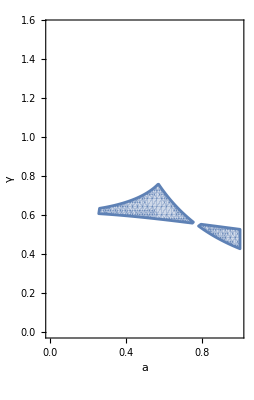

```mathematica
RegionPlot[Xor@@equlibria[[;;,3]],{a,0,1},{γ,0.0001,Pi/2},PlotPoints->40,FrameLabel->{"a","γ"},AspectRatio->Automatic]
```

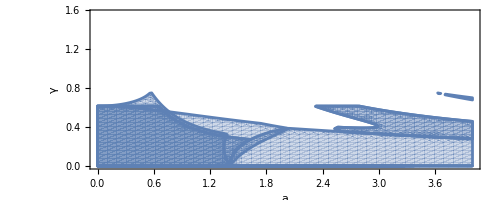

```mathematica
Show[Table[RegionPlot[equlibria[[i,3]],{a,0,4},{γ,0,Pi/2},PlotPoints->40,FrameLabel->{"a","γ"},AspectRatio->Automatic],{i,Length[equlibria]}]]
```

```mathematica
Series[equlibria[[3,3]],{a,0,20}]//Normal
```

a≥0&&8 Cos[2 (-1+a) γ]+Cos[4 a γ]+8 Cos[2 (1+a) γ]+8 Sin[a γ] (7 Cos[2 γ] Sin[a γ]+Sin[γ] Sin[2 a γ])≤17&&33+6 Cos[2 (-1+a) γ]+6 Cos[2 (1+a) γ]≥4 Cos[2 γ]+8 Cos[2 a γ]+Cos[4 a γ]+8 Sin[γ] Sin[a γ] Sin[2 a γ]&&8 Cos[2 γ]+4 Cos[2 (-1+a) γ]+Cos[4 a γ]+4 Cos[2 (1+a) γ]+12 Sin[γ] Sin[a γ] Sin[2 a γ]≤17+16 Cos[2 a γ]&&12 Cos[2 γ]+16 Cos[2 a γ]+Cos[4 a γ]≥1+14 Cos[2 (-1+a) γ]+14 Cos[2 (1+a) γ]+40 Sin[γ] Sin[a γ] Sin[2 a γ]&&6 Cos[2 γ]+3 (Cos[2 (-1+a) γ]+Cos[2 (1+a) γ])+10 Sin[γ] Sin[a γ] Sin[2 a γ]≥4 Cos[a γ]^4&&4 (3 Cos[2 γ]+8 Cos[2 a γ]+6 Sin[γ] Sin[a γ] Sin[2 a γ])≥5+2 Cos[2 (-1+a) γ]+3 Cos[4 a γ]+2 Cos[2 (1+a) γ]&&4 Cos[a γ]^2≥2 Cos[2 γ]+Cos[2 (-1+a) γ]+Cos[2 (1+a) γ]+6 Sin[γ] Sin[a γ] Sin[2 a γ]

```mathematica
Maximize[{Series[equlibria[[3,2,1]],{a,0,2}]//Normal,Series[equlibria[[3,3]],{a,0,2}]//Normal},{a,γ}]
```

Maximize[{2-Cos[2 γ]+1/2 a^2 (γ^2+2 γ^2 Cos[2 γ]-γ^2 Sin[γ]),a≥0&&8 Cos[2 (-1+a) γ]+Cos[4 a γ]+8 Cos[2 (1+a) γ]+8 Sin[a γ] (7 Cos[2 γ] Sin[a γ]+Sin[γ] Sin[2 a γ])≤17&&33+6 Cos[2 (-1+a) γ]+6 Cos[2 (1+a) γ]≥4 Cos[2 γ]+8 Cos[2 a γ]+Cos[4 a γ]+8 Sin[γ] Sin[a γ] Sin[2 a γ]&&8 Cos[2 γ]+4 Cos[2 (-1+a) γ]+Cos[4 a γ]+4 Cos[2 (1+a) γ]+12 Sin[γ] Sin[a γ] Sin[2 a γ]≤17+16 Cos[2 a γ]&&12 Cos[2 γ]+16 Cos[2 a γ]+Cos[4 a γ]≥1+14 Cos[2 (-1+a) γ]+14 Cos[2 (1+a) γ]+40 Sin[γ] Sin[a γ] Sin[2 a γ]&&6 Cos[2 γ]+3 (Cos[2 (-1+a) γ]+Cos[2 (1+a) γ])+10 Sin[γ] Sin[a γ] Sin[2 a γ]≥4 Cos[a γ]^4&&4 (3 Cos[2 γ]+8 Cos[2 a γ]+6 Sin[γ] Sin[a γ] Sin[2 a γ])≥5+2 Cos[2 (-1+a) γ]+3 Cos[4 a γ]+2 Cos[2 (1+a) γ]&&4 Cos[a γ]^2≥2 Cos[2 γ]+Cos[2 (-1+a) γ]+Cos[2 (1+a) γ]+6 Sin[γ] Sin[a γ] Sin[2 a γ]},{a,γ}]

```mathematica
NMaximize[{equlibria[[3,2,1]],equlibria[[3,3]]},{a,γ},WorkingPrecision->60]
equlibria[[3,3]]/.%[[2]]
```

{1.98427231142030744996720851465855234306137250414083659265898,{a→0.571320797534542205294737588081989774973785797334559391296236,γ→0.760424577816584242815516930285634524726638306689022268718116}}

True

```mathematica
equlibria[[3,3]]/.%[[2]]
```

Part::partd: Part specification False⟦2⟧ is longer than depth of object.

ReplaceAll::reps: {False⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

a≥0&&8 Cos[2 (-1+a) γ]+Cos[4 a γ]+8 Cos[2 (1+a) γ]+8 Sin[a γ] (7 Cos[2 γ] Sin[a γ]+Sin[γ] Sin[2 a γ])≤17&&33+6 Cos[2 (-1+a) γ]+6 Cos[2 (1+a) γ]≥4 Cos[2 γ]+8 Cos[2 a γ]+Cos[4 a γ]+8 Sin[γ] Sin[a γ] Sin[2 a γ]&&8 Cos[2 γ]+4 Cos[2 (-1+a) γ]+Cos[4 a γ]+4 Cos[2 (1+a) γ]+12 Sin[γ] Sin[a γ] Sin[2 a γ]≤17+16 Cos[2 a γ]&&12 Cos[2 γ]+16 Cos[2 a γ]+Cos[4 a γ]≥1+14 Cos[2 (-1+a) γ]+14 Cos[2 (1+a) γ]+40 Sin[γ] Sin[a γ] Sin[2 a γ]&&6 Cos[2 γ]+3 (Cos[2 (-1+a) γ]+Cos[2 (1+a) γ])+10 Sin[γ] Sin[a γ] Sin[2 a γ]≥4 Cos[a γ]^4&&4 (3 Cos[2 γ]+8 Cos[2 a γ]+6 Sin[γ] Sin[a γ] Sin[2 a γ])≥5+2 Cos[2 (-1+a) γ]+3 Cos[4 a γ]+2 Cos[2 (1+a) γ]&&4 Cos[a γ]^2≥2 Cos[2 γ]+Cos[2 (-1+a) γ]+Cos[2 (1+a) γ]+6 Sin[γ] Sin[a γ] Sin[2 a γ]/.False⟦2⟧

```mathematica
Table[
m = NMaximize[{equlibria[[i,2,1]],equlibria[[i,3]]&&0<=γ<=Pi/2},{a,γ}];

{equlibria[[i,1]],equlibria[[i,2]]/.m[[2]],m}//N,{i,Length[equlibria]}]//MatrixForm
```

((4.
8.) | (2.40958
1.) | (2.40958
{a→2.60411,γ→0.352131})
(5.
8.) | (1.92095
1.66667) | (1.92095
{a→4.4523,γ→0.615482})
(6.
6.) | (1.98427
1.98427) | (1.98427
{a→0.571321,γ→0.760425})
(6.
8.) | (1.46533
0.999998) | (1.46533
{a→811.764,γ→0.293519})
(7.
7.) | (1.98427
1.98427) | (1.98427
{a→3.56004,γ→0.760425})
(7.
8.) | (1.46532
1.) | (1.46532
{a→51.8381,γ→0.293519})
(8.
4.) | (1.66667
1.69474) | (1.66667
{a→257.979,γ→0.61548})
(8.
5.) | (1.66667
1.6673) | (1.66667
{a→45.907,γ→0.61548})
(8.
6.) | (1.
1.0951) | (1.
{a→139.048,γ→0.137001})
(8.
7.) | (1.
1.) | (1.
{a→1.36443,γ→0.000167082})
(8.
8.) | (1.
1.) | (1.
{a→0.566547,γ→0.0000264044}))

```mathematica
Table[

{equlibria[[i,1]],equlibria[[i,2]]/.{a->3.5600443633150483,γ->0.7604248448225631},equlibria[[i,3]]/.{a->3.5600443633150483,γ->0.7604248448225631}}//N,{i,Length[equlibria]}]//MatrixForm
```

```mathematica
scores
```

scores

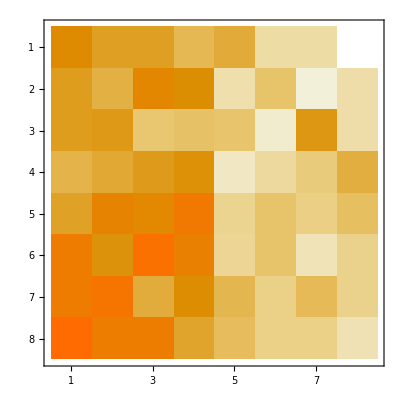

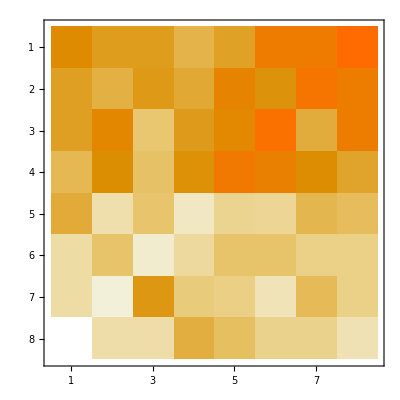

```mathematica
MatrixPlot[alicesScores/.{a->0.57132079753454220529473758808198977497378579733455939129623561893721875401471`60.,γ->0.76042457781658424281551693028563452472663830668902226871811610809250807181883`60.}]
MatrixPlot[bobsScores/.{a->0.57132079753454220529473758808198977497378579733455939129623561893721875401471`60.,γ->0.76042457781658424281551693028563452472663830668902226871811610809250807181883`60.}]
```

```mathematica
equlibria/.{a->0.57132079753454220529473758808198977497378579733455939129623561893721875401471`60.,γ->0.76042457781658424281551693028563452472663830668902226871811610809250807181883`60.}//MatrixForm
```

({4,8} | {2.5052761023038757222652950876042267535283789217972783496855,2.2998698231320063371012115629640942524507877545956453856625} | False
{5,8} | {2.0696135072735933709186226016955651957711778222509340381659,2.0253877545205657788029804953363911991835798426251923760174} | False
{6,6} | {1.984272311420307449967208514658552343061372504140836592659,1.984272311420307449967208514658552343061372504140836592659} | True
{6,8} | {1.534806753636796685459311300847782597885588911125467019083,1.5126938772602828894014902476681955995917899213125961880087} | False
{7,7} | {2.09503544906004360152455837278284090080545182581044174545565,2.09503544906004360152455837278284090080545182581044174545565} | False
{7,8} | {1.534806753636796685459311300847782597885588911125467019083,1.5126938772602828894014902476681955995917899213125961880087} | False
{8,4} | {2.2998698231320063371012115629640942524507877545956453856625,2.5052761023038757222652950876042267535283789217972783496855} | False
{8,5} | {2.0253877545205657788029804953363911991835798426251923760174,2.0696135072735933709186226016955651957711778222509340381659} | False
{8,6} | {1.5126938772602828894014902476681955995917899213125961880087,1.534806753636796685459311300847782597885588911125467019083} | False
{8,7} | {1.5126938772602828894014902476681955995917899213125961880087,1.534806753636796685459311300847782597885588911125467019083} | False
{8,8} | {1,1} | False)

```mathematica
Table[m = NMaximize[{equlibria[[i,2,2]],equlibria[[i,3]]&&0<=γ<=Pi/2},{a,γ}];

{equlibria[[i,1]],equlibria[[i,2]]/.m[[2]],m}//N,{i,Length[equlibria]}]//MatrixForm
```

((4.
8.) | (1.67027
1.66667) | (1.66667
{a→870.359,γ→0.61548})
(5.
8.) | (1.91833
1.66667) | (1.66667
{a→1147.82,γ→0.61548})
(6.
6.) | (1.98427
1.98427) | (1.98427
{a→0.571321,γ→0.760425})
(6.
8.) | (1.02367
1.) | (1.
{a→1.42547,γ→0.0686991})
(7.
7.) | (1.98427
1.98427) | (1.98427
{a→3.56004,γ→0.760425})
(7.
8.) | (1.
1.) | (1.
{a→0.0138274,γ→1.71235×10^-6})
(8.
4.) | (1.
2.40958) | (2.40958
{a→2.60411,γ→0.352131})
(8.
5.) | (1.66668
1.92095) | (1.92095
{a→9.5565,γ→0.615487})
(8.
6.) | (1.
1.46532) | (1.46532
{a→1.67786,γ→0.293519})
(8.
7.) | (1.
1.46532) | (1.46532
{a→1207.78,γ→0.293519})
(8.
8.) | (1.
1.) | (1.
{a→0.566547,γ→0.0000264044}))

```mathematica
bothScores/.a->0//FullSimplify//MatrixForm
```

((3
3) | (1/2 (5+Cos[2 γ])
1/2 (5+Cos[2 γ])) | (1/2 (5+Cos[2 γ])
1/2 (5+Cos[2 γ])) | (2+Cos[2 γ]
2+Cos[2 γ]) | (5 Sin[γ]^2
5 Cos[γ]^2) | ((5 Sin[γ]^2)/2
5/4 (3+Cos[2 γ])) | ((5 Sin[γ]^2)/2
5/4 (3+Cos[2 γ])) | (0
5)
(1/2 (5+Cos[2 γ])
1/2 (5+Cos[2 γ])) | (2+Cos[2 γ]
2+Cos[2 γ]) | (3
3) | (1/2 (5+Cos[2 γ])
1/2 (5+Cos[2 γ])) | ((5 Sin[γ]^2)/2
5/4 (3+Cos[2 γ])) | (5 Sin[γ]^2
5 Cos[γ]^2) | (0
5) | ((5 Sin[γ]^2)/2
5/4 (3+Cos[2 γ]))
(1/2 (5+Cos[2 γ])
1/2 (5+Cos[2 γ])) | (3
3) | (2+Cos[2 γ]
2+Cos[2 γ]) | (1/2 (5+Cos[2 γ])
1/2 (5+Cos[2 γ])) | ((5 Sin[γ]^2)/2
5/4 (3+Cos[2 γ])) | (0
5) | (5 Sin[γ]^2
5 Cos[γ]^2) | ((5 Sin[γ]^2)/2
5/4 (3+Cos[2 γ]))
(2+Cos[2 γ]
2+Cos[2 γ]) | (1/2 (5+Cos[2 γ])
1/2 (5+Cos[2 γ])) | (1/2 (5+Cos[2 γ])
1/2 (5+Cos[2 γ])) | (3
3) | (0
5) | ((5 Sin[γ]^2)/2
5/4 (3+Cos[2 γ])) | ((5 Sin[γ]^2)/2
5/4 (3+Cos[2 γ])) | (5 Sin[γ]^2
5 Cos[γ]^2)
(5 Cos[γ]^2
5 Sin[γ]^2) | (5/4 (3+Cos[2 γ])
(5 Sin[γ]^2)/2) | (5/4 (3+Cos[2 γ])
(5 Sin[γ]^2)/2) | (5
0) | (1
1) | (1/2 (3-Cos[2 γ])
1/2 (3-Cos[2 γ])) | (1/2 (3-Cos[2 γ])
1/2 (3-Cos[2 γ])) | (2-Cos[2 γ]
2-Cos[2 γ])
(5/4 (3+Cos[2 γ])
(5 Sin[γ]^2)/2) | (5 Cos[γ]^2
5 Sin[γ]^2) | (5
0) | (5/4 (3+Cos[2 γ])
(5 Sin[γ]^2)/2) | (1/2 (3-Cos[2 γ])
1/2 (3-Cos[2 γ])) | (2-Cos[2 γ]
2-Cos[2 γ]) | (1
1) | (1/2 (3-Cos[2 γ])
1/2 (3-Cos[2 γ]))
(5/4 (3+Cos[2 γ])
(5 Sin[γ]^2)/2) | (5
0) | (5 Cos[γ]^2
5 Sin[γ]^2) | (5/4 (3+Cos[2 γ])
(5 Sin[γ]^2)/2) | (1/2 (3-Cos[2 γ])
1/2 (3-Cos[2 γ])) | (1
1) | (2-Cos[2 γ]
2-Cos[2 γ]) | (1/2 (3-Cos[2 γ])
1/2 (3-Cos[2 γ]))
(5
0) | (5/4 (3+Cos[2 γ])
(5 Sin[γ]^2)/2) | (5/4 (3+Cos[2 γ])
(5 Sin[γ]^2)/2) | (5 Cos[γ]^2
5 Sin[γ]^2) | (2-Cos[2 γ]
2-Cos[2 γ]) | (1/2 (3-Cos[2 γ])
1/2 (3-Cos[2 γ])) | (1/2 (3-Cos[2 γ])
1/2 (3-Cos[2 γ])) | (1
1))